### Element force archive (manually select element)

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\element_stiffness";
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1";

estifffile="Ke_by_element.xlsx";
connfile="connectivity_Q9_40x40.xlsx";
dispfile="nodal_displacement_disp_control_(1,1).xlsx";

estiffdata=Import[FileNameJoin[{dir,estifffile}]];
conndata=Import[FileNameJoin[{dir2,connfile}]];
dispdata=Import[FileNameJoin[{dir2,dispfile}]];

elemid=0; (*Python 0-based*)
(*Element stiffness matrix*)
estiffness=estiffdata[[elemid+1]]; (*elem stiffness matrix*)
estiffness=Drop[Drop[estiffness,{1,6}],None,{1,1}]; (*remove all redundant rows and columns*)
(*Connectivity matrix*)
connmatrix=Drop[Drop[conndata[[1]],1],None,1]; (*conn matrix*)
elemnodeid=connmatrix[[elemid+1]]; (*extract element nodes id*)
(*Nodal disp*)
nodaldata=Drop[dispdata[[1]],1]; (*nodal data with heading*)
nodalsol=nodaldata[[elemnodeid+1]]; (*All nodal solution: U, RF*)
nodaldisp=nodalsol[[All,{4,5}]]; (*only displacment results*)
nodaldispflatten=nodaldisp//Flatten; (*flatten to make dofs compatible with estiffness *)

(* Get element nodal forces *)
elemforce=estiffness.nodaldispflatten//MatrixForm
```

### Element force v2 (with element_id as input)

```mathematica
Clear["Global`*"]
```

```mathematica
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\element_stiffness";
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,1,1,1,10)_dz=-0.1";
estifffile="Ke_by_element.xlsx";
connfile="connectivity_Q9_40x40.xlsx";
dispfile="nodal_displacement_disp_control_(1,1).xlsx";

estiffdata=Import[FileNameJoin[{dir,estifffile}]];
conndata=Import[FileNameJoin[{dir2,connfile}]];
dispdata=Import[FileNameJoin[{dir2,dispfile}]];
```

```mathematica
(*connectivity without headers (same idea as your earlier snippet)*)
connmatrix=Drop[Drop[conndata[[1]],1],None,1];
(*nodal table without header row*)
nodaldata=Drop[dispdata[[1]],1];
(* =========================Functions=========================*)

ClearAll[estiffness,elemnodeid,nodaldispvec,elemforce];
(*Element stiffness matrix with redundant rows/cols removed*)
estiffness[elemid_Integer]:=Drop[Drop[estiffdata[[elemid+1]],{1,6}],None,{1,1}];
(*Element node IDs (Python 0-based stored in file)*)
elemnodeid[elemid_Integer]:=connmatrix[[elemid+1]];
(*Flattened displacement vector compatible with Ke*)
nodaldispvec[elemid_Integer]:=Module[{elemnode,nodalsol,nodaldisp},elemnode=elemnodeid[elemid];
nodalsol=nodaldata[[elemnode+1]];(*+1 because Mathematica is 1-based*)nodaldisp=nodalsol[[All,{4,5}]];(*columns Ux,Uy*)Flatten[nodaldisp]];
(*Element nodal force vector*)
elemforce[elemid_Integer]:=estiffness[elemid].nodaldispvec[elemid];
```

```mathematica
Partition[elemforce[1],2]//MatrixForm
Partition[elemforce[2],2]//MatrixForm
```

(257430. | 469243.
-35017.1 | 197044.
-176342. | -397680.
-37805. | -256523.
384819. | 1.26353×10^6
-421534. | -369925.
-366557. | -1.31035×10^6
395005. | 404656.
-4.65661×10^-10 | -2.91038×10^-10)

(216223. | 384865.
-34521.8 | 185458.
-173218. | -359845.
-8539.36 | -209866.
339289. | 1.11444×10^6
-412599. | -331604.
-348167. | -1.15338×10^6
421534. | 369925.
-4.65661×10^-10 | -5.82077×10^-11)

```mathematica
Ne=Length[connmatrix];  (*number of elements*)

forceMat=Table[Prepend[Flatten@elemforce[e],e],(*add elemid (0-based) as first column*){e,0,Ne-1}];

header18=Flatten@Table[{"f"<>ToString[i]<>"_1","f"<>ToString[i]<>"_2"},{i,1,9}];

header19=Prepend[header18,"elemid(py0)"];

Export[FileNameJoin[{dir2,"ElementForce.xlsx"}],Prepend[forceMat,header19],"XLSX"];
```

#### Traction along horizontal plane y=0.25

```mathematica
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
elenodalforce="ElementForce.xlsx";
elenodalforcedata=Import[FileNameJoin[{dir2,elenodalforce}]];

eleforcedata=Drop[Drop[elenodalforcedata[[1]],{1,1}],{1,1}];
fyrow1=Take[eleforcedata[[All,{9,15,7}]],40];
fxrow1=Take[eleforcedata[[All,{8,14,6}]],40];

Ne=Length[fyrow1];
Fgxrow1=ConstantArray[0,2 Ne+1];
Fgyrow1=ConstantArray[0,2 Ne+1];

Do[
Fgxrow1[[{2 e-1,2 e,2 e+1}]]+=fxrow1[[e]];
Fgyrow1[[{2 e-1,2 e,2 e+1}]]+=fyrow1[[e]];
,{e,1,40}];
```

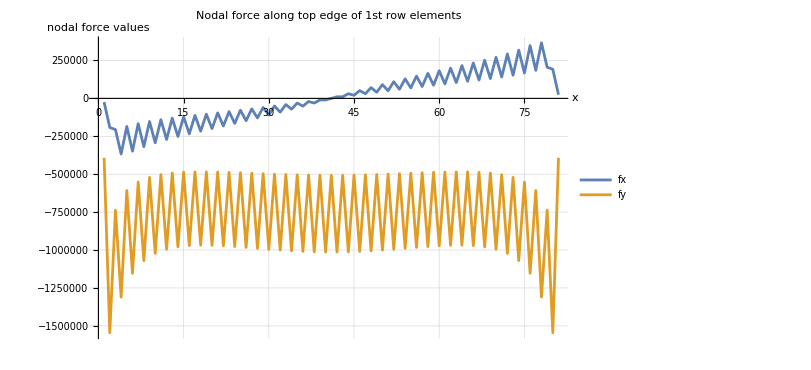

```mathematica
ListLinePlot[{Fgxrow1,Fgyrow1},PlotRange->All,PlotLegends->Placed[{Style["fx",16],Style["fy",16]},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along top edge of 1st row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

```mathematica
(*
Comments: 
- fy is symmetric along the mid plane of the domain, which is expected;
 - fx is skew-symmetric along the mid plane of the domain, which is expected;
 - insight about nodal force distribution: for the fy nodal for, at the edge we have high value but does not means the traction is high;
 - There are mixed boundary condition feature at the two outer edge.
*)
```

#### Traction along horizontal plane y=9.25 & 9.75

{874.559,10012.1,5828.84,9433.15,3499.19,5048.85,1548.87,1752.11,262.038,-419.427,-565.498,-1866.08,-1126.57,-2934.77,-1569.47,-3916.55,-2026.15,-5125.65,-2660.65,-7050.54,-3765.95,-10720.3,-6023.82,-18821.4,-11377.1,-39889.2,-26888.2,-109364.,-91501.5,-443217.,-569778.,-2.97312×10^6,-2.71762×10^6,-5.68147×10^6,-2.64125×10^6,-4.40261×10^6,-1.96464×10^6,-3.69016×10^6,-1.75115×10^6,-3.43339×10^6,-1.69414×10^6,-3.43339×10^6,-1.75115×10^6,-3.69016×10^6,-1.96464×10^6,-4.40261×10^6,-2.64125×10^6,-5.68147×10^6,-2.71762×10^6,-2.97312×10^6,-569778.,-443217.,-91501.5,-109364.,-26888.2,-39889.2,-11377.1,-18821.4,-6023.82,-10720.3,-3765.95,-7050.54,-2660.65,-5125.65,-2026.15,-3916.55,-1569.47,-2934.77,-1126.57,-1866.08,-565.498,-419.427,262.038,1752.11,1548.87,5048.85,3499.19,9433.15,5828.84,10012.1,874.559}

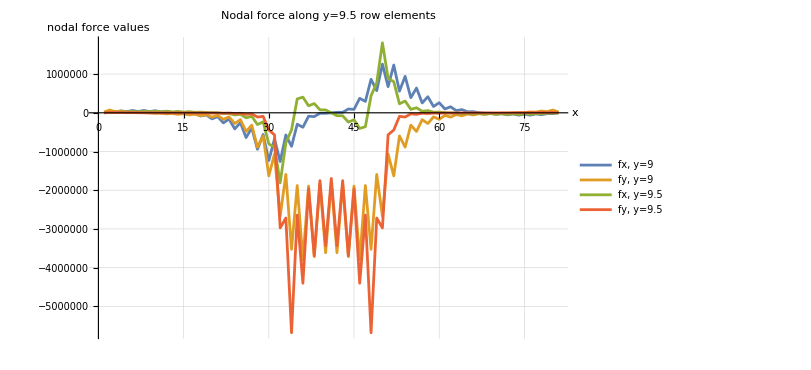

```mathematica
fxY9=Take[eleforcedata[[All,{8,14,6}]],{1441,1480}];
fyY9=Take[eleforcedata[[All,{9,15,7}]],{1441,1480}];

Ne=Length[fxY9];
FgxY9=ConstantArray[0,2 Ne+1];
FgyY9=ConstantArray[0,2 Ne+1];

Do[
FgxY9[[{2 e-1,2 e,2 e+1}]]+=fxY9[[e]];
FgyY9[[{2 e-1,2 e,2 e+1}]]+=fyY9[[e]];
,{e,1,40}];

fxY95=Take[eleforcedata[[All,{8,14,6}]],{1521,1560}]; (*top edges of second row from the top*)
fyY95=Take[eleforcedata[[All,{9,15,7}]],{1521,1560}]; (*top edge of second row from the top*)

Ne=Length[fxY95];
FgxY95=ConstantArray[0,2 Ne+1];
FgyY95=ConstantArray[0,2 Ne+1];

Do[
FgxY95[[{2 e-1,2 e,2 e+1}]]+=fxY95[[e]];
FgyY95[[{2 e-1,2 e,2 e+1}]]+=fyY95[[e]];
,{e,1,40}];
FgyY95

ListLinePlot[{FgxY9,FgyY9,FgxY95,FgyY95},PlotRange->All,
PlotLegends->Placed[{
Style["fx, y=9",16],Style["fy,  y=9",16],
Style["fx, y=9.5",16],Style["fy,  y=9.5",16]
},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along y=9.5 row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

#### Traction along horizontal plane y=9.5

{8931.19,36150.4,16733.,27202.9,10382.,14592.7,4450.08,4149.4,-27.9439,-3645.01,-3345.51,-9656.98,-6026.23,-14965.9,-8621.09,-20764.7,-11776.9,-28657.4,-16466.4,-41394.6,-24520.1,-64667.4,-39986.8,-112022.,-73091.4,-219928.,-153340.,-497534.,-376277.,-1.26927×10^6,-983136.,-2.89096×10^6,-1.90188×10^6,-4.26303×10^6,-2.21277×10^6,-4.2119×10^6,-2.00245×10^6,-3.80064×10^6,-1.82444×10^6,-3.57601×10^6,-1.76848×10^6,-3.57601×10^6,-1.82444×10^6,-3.80064×10^6,-2.00245×10^6,-4.2119×10^6,-2.21277×10^6,-4.26303×10^6,-1.90188×10^6,-2.89096×10^6,-983136.,-1.26927×10^6,-376277.,-497534.,-153340.,-219928.,-73091.4,-112022.,-39986.8,-64667.4,-24520.1,-41394.6,-16466.4,-28657.4,-11776.9,-20764.7,-8621.09,-14965.9,-6026.23,-9656.98,-3345.51,-3645.01,-27.9439,4149.4,4450.08,14592.7,10382.,27202.9,16733.,36150.4,8931.19}

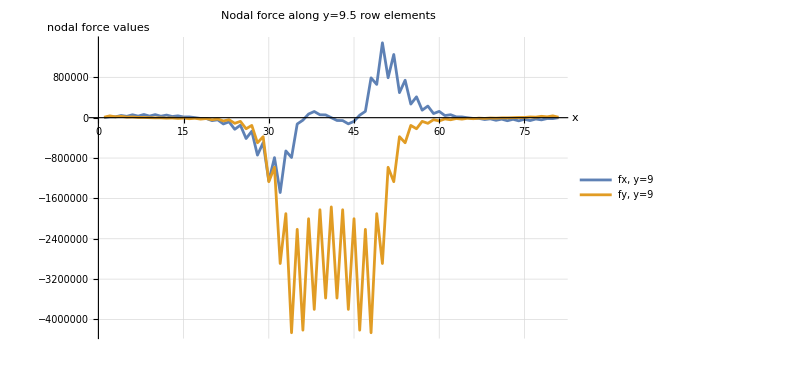

```mathematica
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
elenodalforce="ElementForce.xlsx";
elenodalforcedata=Import[FileNameJoin[{dir2,elenodalforce}]];

eleforcedata=Drop[Drop[elenodalforcedata[[1]],{1,1}],{1,1}];
fxY95=Take[eleforcedata[[All,{8,14,6}]],{1481,1520}]; (*top edges of second row from the top*)
fyY95=Take[eleforcedata[[All,{9,15,7}]],{1481,1520}]; (*top edge of second row from the top*)

Ne=Length[fxY95];
FgxY95=ConstantArray[0,2 Ne+1];
FgyY95=ConstantArray[0,2 Ne+1];

Do[
FgxY95[[{2 e-1,2 e,2 e+1}]]+=fxY95[[e]];
FgyY95[[{2 e-1,2 e,2 e+1}]]+=fyY95[[e]];
,{e,1,40}];
FgyY95

ListLinePlot[{FgxY95,FgyY95},PlotRange->All,
PlotLegends->Placed[{
Style["fx, y=9",16],Style["fy,  y=9",16],
Style["fx, y=9.5",16],Style["fy,  y=9.5",16]
},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along y=9.5 row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

#### Traction along horizontal plane y=5

{-105881.,-447802.,-236550.,-500585.,-264433.,-558803.,-294683.,-621197.,-326764.,-686830.,-360269.,-754982.,-394879.,-825056.,-430310.,-896495.,-466280.,-968706.,-502474.,-1.041×10^6,-538517.,-1.11255×10^6,-573955.,-1.18238×10^6,-608259.,-1.24934×10^6,-640820.,-1.31216×10^6,-670977.,-1.36948×10^6,-698037.,-1.41993×10^6,-721316.,-1.46216×10^6,-740180.,-1.49501×10^6,-754081.,-1.51748×10^6,-762599.,-1.52889×10^6,-765469.,-1.52889×10^6,-762599.,-1.51748×10^6,-754081.,-1.49501×10^6,-740180.,-1.46216×10^6,-721316.,-1.41993×10^6,-698037.,-1.36948×10^6,-670977.,-1.31216×10^6,-640820.,-1.24934×10^6,-608259.,-1.18238×10^6,-573955.,-1.11255×10^6,-538517.,-1.041×10^6,-502474.,-968706.,-466280.,-896495.,-430310.,-825056.,-394879.,-754982.,-360269.,-686830.,-326764.,-621197.,-294683.,-558803.,-264433.,-500585.,-236550.,-447802.,-105881.}

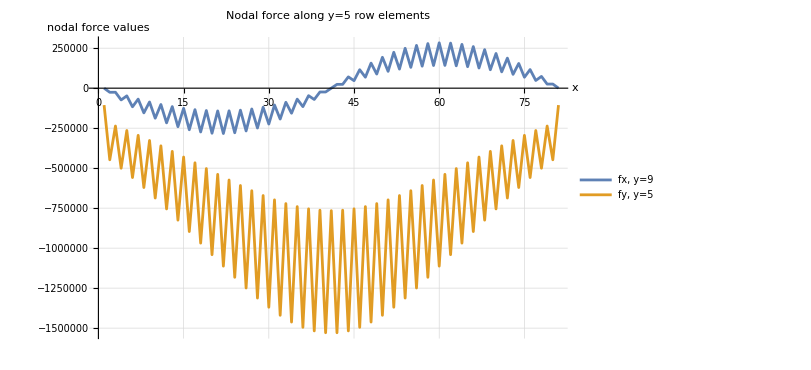

```mathematica
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
elenodalforce="ElementForce.xlsx";
elenodalforcedata=Import[FileNameJoin[{dir2,elenodalforce}]];

eleforcedata=Drop[Drop[elenodalforcedata[[1]],{1,1}],{1,1}];
fxY95=Take[eleforcedata[[All,{8,14,6}]],{761,800}]; (*top edges of second row from the top*)
fyY95=Take[eleforcedata[[All,{9,15,7}]],{761,800}]; (*top edge of second row from the top*)

Ne=Length[fxY95];
FgxY95=ConstantArray[0,2 Ne+1];
FgyY95=ConstantArray[0,2 Ne+1];

Do[
FgxY95[[{2 e-1,2 e,2 e+1}]]+=fxY95[[e]];
FgyY95[[{2 e-1,2 e,2 e+1}]]+=fyY95[[e]];
,{e,1,40}];
FgyY95

ListLinePlot[{FgxY95,FgyY95},PlotRange->All,
PlotLegends->Placed[{
Style["fx, y=9",16],Style["fy,  y=5",16],
Style["fx, y=9.5",16],Style["fy,  y=5",16]
},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along y=5 row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

#### Functions to invert from nodal force to traction

```mathematica
Clear["Global`*"]
(*Gamma function and its values at zero*)
γ[η_,m_,n_]:=Abs[1-(1-((η+1)/2)^2)^m]^n
γ01[m_,n_]:=γ[0,m,n]
γ02[m_,n_]:=γ[0,m,n]
NAG3one[η_,m_,n_]:=(-γ01[m,n]+(γ01[m,n]-1) η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3two[η_,m_,n_]:=(1+η-2 γ[η,m,n])/(1-2 γ01[m,n])
NAG3three[η_,m_,n_]:=(-γ01[m,n]-γ01[m,n] η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3t2one[η_,m_,n_]:=NAG3three[-η,m,n]
NAG3t2two[η_,m_,n_]:=NAG3two[-η,m,n]
NAG3t2three[η_,m_,n_]:=NAG3one[-η,m,n]
(*Shape function for AG type 1*)
NShape[η_,m_,n_]:={NAG3one[η,m,n],NAG3two[η,m,n],NAG3three[η,m,n]};
dNShape[η_,m_,n_]:=D[NShape[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(*Shape function for AG type 2*)
NShape2[η_,m_,n_]:={NAG3t2one[η,m,n],NAG3t2two[η,m,n],NAG3t2three[η,m,n]};
dNShape2[η_,m_,n_]:=D[NShape2[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(***************************************************************)
(*Function to get the M matrices: relate Nodal force and Nodal traction*)
elementMmatrix[xpos_,AGtype_]:= Module[{},
{m,n,type}={AGtype[[1]],AGtype[[2]],AGtype[[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
(*Print[AGshape[η,m,n]];*)
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
M=Table[NIntegrate[AGshape[η,m,n][[j]]*AGshape[η,m,n][[i]]*jac,{η,-1,1}],{i,1,3},{j,1,3}]
];
(***************************************************************)
(*Function Global M matrices: relate Global Nodal force and Nodal traction*)
GlobalMmat[xcoord_,conns_,AGtype_]:=Module[{n=Max@Flatten@conns,GlobalMat,Me,conn},
GlobalMat=ConstantArray[0.,{n,n}];
Do[
Me=elementMmatrix[xcoord[[e]],AGtype[[e]]];
(*Print[Me//MatrixForm];*)
conn=conns[[e]];
Do[
GlobalMat[[conn[[i]],conn[[j]]]]+=Me[[i,j]],{i,3},{j,3}],
{e,Length@conns}];
GlobalMat  (* <--return M assembled*)
]
(***************************************************************)
(*Function Global M matrices: relate Global Nodal force and Nodal traction*)
PxinterpolatedData[Pvec_,AGtype_,xcoord_]:=Module[{},
Pxdata={};
(*total=0;*)
Pelem=Partition[Pvec,3,2];
nelem= Length[conns];
Do[
elem=e;
{m,n,type}={AGtype[[elem]][[1]],AGtype[[elem]][[2]],AGtype[[elem]][[5]]};
If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
Clear[x,η];
xη=AGshape[η,1,1].xcoord[[elem]];
ηmap=η/.NSolve[xη==x,η]//First;
PinterpolatePhysical=Sum[AGshape[η,m,n][[i]]*Pelem[[elem]][[i]],{i,1,3}]/.{η->ηmap};(*geometric mapping*)
(*resultant=NIntegrate[PinterpolatePhysical,{x,xmin,xmax}];
PxResultant=total+resultant;*)

{xmin,xmax}={Min[xcoord[[elem]]],Max[xcoord[[elem]]]};
n=100;
dx=(xmax-xmin)/n;
xdata=Table[xmin+i dx,{i,0,n}];
pdata=PinterpolatePhysical/.x->xdata;
plotdata=Transpose[{xdata, pdata}];
Pxdata=AppendTo[Pxdata, plotdata];
,{e,1,nelem}];
Print[PxResultant];
Flatten[Pxdata,1]
]


ComputeResultant[Pelem_,xcoord_,AGtype_]:=Module[{},
totalResutant=0;
Do[
elem=e;
xpos=xcoord[[elem]];
{m,n,type}={AGtype[[elem]][[1]],AGtype[[elem]][[2]],AGtype[[elem]][[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];

resultant=Pelem[[elem]].NIntegrate[AGshape[η,m,n]*jac,{η,-1,1}];
(*Print[resultant];*)
totalResutant=totalResutant+resultant;
,{e,1,Length[conns]}];
totalResutant
]
```

#### p(x) y=9.75 Frictionless punch_Geom 10x10, 40x40 mesh (m1,n1,m2,n2;ngauss)(1,1,1,1;3)

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[1;;81]];
xcoordglobal=underpunchdata[[All,2]];
Fy={874.5585379246622,10012.066707469523,5828.837214931846,9433.14819746092,3499.190758327022,5048.849882092327,1548.8654054701328,1752.1068527530879,262.037510111928,-419.4269038606435,-565.4979969430715,-1866.078010732308,-1126.5741941481829,-2934.768232975155,-1569.473992453888,-3916.5542440004647,-2026.1494517568499,-5125.653418134898,-2660.645878314972,-7050.538168698549,-3765.946733383462,-10720.254240475595,-6023.818817406893,-18821.385634176433,-11377.13286681287,-39889.16538722068,-26888.222640741616,-109364.12359185517,-91501.51494437829,-443216.99130116403,-569778.0549563803,-2.9731210739717856*^6,-2.7176165933358185*^6,-5.681472530769251*^6,-2.641249089443933*^6,-4.402614017195217*^6,-1.9646400330669358*^6,-3.6901600986486003*^6,-1.751153557897061*^6,-3.433393641034119*^6,-1.6941394243013598*^6,-3.4333936410341263*^6,-1.7511535578969605*^6,-3.690160098648511*^6,-1.9646400330667794*^6,-4.402614017194971*^6,-2.6412490894435644*^6,-5.681472530768432*^6,-2.7176165933354944*^6,-2.973121073971458*^6,-569778.0549562667,-443216.99130117893,-91501.51494431868,-109364.12359180301,-26888.222640704364,-39889.165387265384,-11377.132866811007,-18821.385634362698,-6023.818817451596,-10720.254240490496,-3765.9467334225774,-7050.538168799132,-2660.6458782963455,-5125.653418153524,-2026.1494517102838,-3916.554243963212,-1569.4739924632013,-2934.768233049661,-1126.5741941416636,-1866.0780108310282,-565.4979969328269,-419.42690392397344,262.0375100951642,1752.106852741912,1548.8654054785147,5048.849882142618,3499.190758343786,9433.14819746837,5828.837214957923,10012.066707458347,874.5585379200056};
```

PxResultant

Nodal traction vectors P(1,1) = {8802.876,66165.665,62595.808,57855.863,40546.180,30480.234,18542.938,10368.953,3631.848,-2860.271,-5915.294,-11723.440,-12261.864,-18338.664,-17114.920,-24488.039,-21974.025,-32104.976,-28725.372,-44154.552,-41070.499,-66591.063,-69416.247,-113528.354,-151640.057,-223620.490,-452745.950,-541811.966,-1.775×10^6,-2.097×10^6,-8.042×10^6,-1.720×10^7,-3.277×10^7,-3.457×10^7,-3.156×10^7,-2.607×10^7,-2.404×10^7,-2.202×10^7,-2.118×10^7,-2.055×10^7,-2.043×10^7,-2.055×10^7,-2.118×10^7,-2.202×10^7,-2.404×10^7,-2.607×10^7,-3.156×10^7,-3.457×10^7,-3.277×10^7,-1.720×10^7,-8.042×10^6,-2.097×10^6,-1.775×10^6,-541811.966,-452745.950,-223620.490,-151640.057,-113528.354,-69416.247,-66591.063,-41070.499,-44154.552,-28725.372,-32104.976,-21974.025,-24488.039,-17114.920,-18338.664,-12261.864,-11723.440,-5915.294,-2860.271,3631.848,10368.953,18542.938,30480.234,40546.180,57855.863,62595.808,66165.665,8802.876}

p(x) resultant force P(1,1) = -6.28497×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2026_01_21_analysis element nodal force, traction\2026_01_21_punch_results\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)\NodalTraction.xlsx

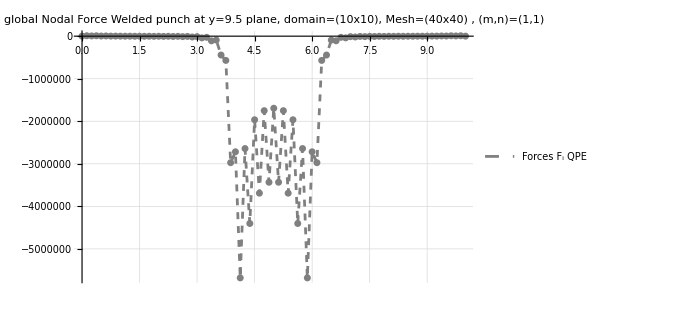

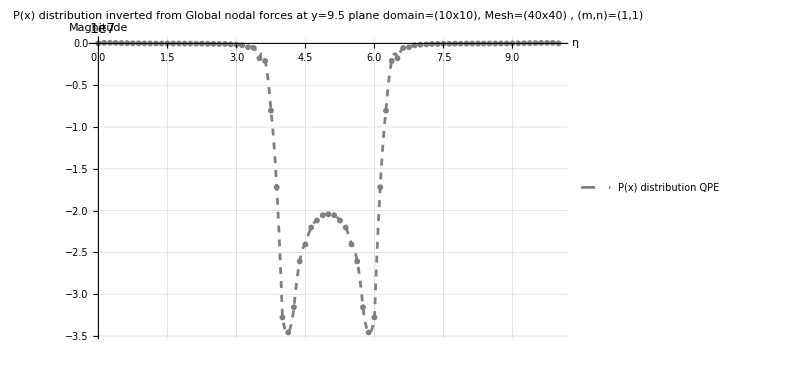

```mathematica
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=40; (*For*)
{m1,n1,m2,n2}={1,1,1,1};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 1};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];

(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{All,All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch at y=9.5 plane, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]

(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.007]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE]
```

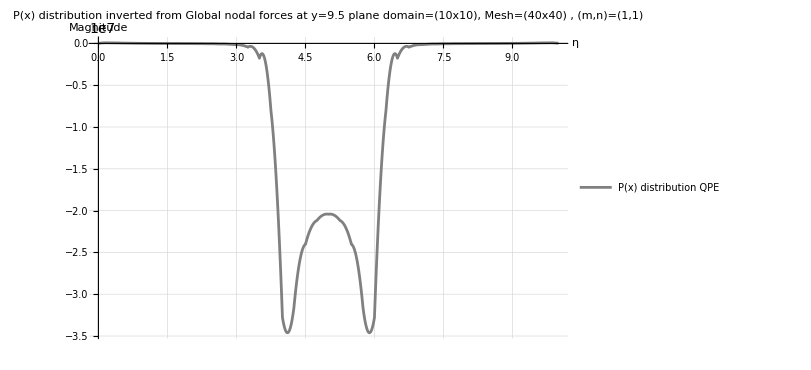

```mathematica
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
```

#### p(x) y=9.5 Frictionless punch_Geom 10x10, 40x40 mesh (m1,n1,m2,n2;ngauss)(1,1,1,1;3)

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[1;;81]];
xcoordglobal=underpunchdata[[All,2]];
Fy={8931.194194601849,36150.387278262526,16732.993409309536,27202.933679083362,10381.975375056267,14592.732172805816,4450.079402578995,4149.396912202239,-27.94385534338653,-3645.007299689576,-3345.510621391237,-9656.982449194416,-6026.228433556855,-14965.903125721961,-8621.08869804442,-20764.664911091328,-11776.861477453262,-28657.36374413222,-16466.397777818143,-41394.615812167525,-24520.09788416885,-64667.440345000476,-39986.75515749678,-112021.6798434928,-73091.39986522123,-219928.49225667492,-153340.09677758627,-497534.0016511269,-376276.7581142727,-1.2692700558359697*^6,-983136.1091124676,-2.890955975348592*^6,-1.90188406903857*^6,-4.263028403577238*^6,-2.212771439910911*^6,-4.21189800033918*^6,-2.0024462205932736*^6,-3.8006359167495966*^6,-1.8244359157051556*^6,-3.576010580680676*^6,-1.7684847469690442*^6,-3.5760105806806684*^6,-1.8244359157050252*^6,-3.800635916749522*^6,-2.0024462205930986*^6,-4.211898000338897*^6,-2.2127714399107993*^6,-4.263028403576903*^6,-1.9018840690387934*^6,-2.8909559753483757*^6,-983136.1091124509,-1.2692700558359437*^6,-376276.75811426155,-497534.00165107474,-153340.09677760117,-219928.49225670844,-73091.39986521564,-112021.67984357476,-39986.755157541484,-64667.440345175564,-24520.097884200513,-41394.6158121489,-16466.397777814418,-28657.36374410987,-11776.861477475613,-20764.664911024272,-8621.088698040694,-14965.903125774115,-6026.228433559649,-9656.982449114323,-3345.510621362366,-3645.0072996914387,-27.943855308927596,4149.396912200376,4450.079402573407,14592.732172846794,10381.975375075825,27202.933679126203,16732.993409316987,36150.38727821596,8931.194194590673};
```

PxResultant

Nodal traction vectors P(1,1) = {206587.686,220782.811,196173.062,163959.973,124323.171,87074.555,54644.320,24134.852,1240.678,-22684.518,-38464.968,-58808.579,-70485.344,-90758.131,-101403.796,-125674.546,-139079.731,-173100.233,-195560.231,-249248.187,-294131.223,-387234.102,-488042.383,-664699.298,-915664.022,-1.288×10^6,-1.973×10^6,-2.884×10^6,-4.809×10^6,-7.424×10^6,-1.196×10^7,-1.738×10^7,-2.248×10^7,-2.589×10^7,-2.621×10^7,-2.531×10^7,-2.405×10^7,-2.275×10^7,-2.200×10^7,-2.140×10^7,-2.133×10^7,-2.140×10^7,-2.200×10^7,-2.275×10^7,-2.405×10^7,-2.531×10^7,-2.621×10^7,-2.589×10^7,-2.248×10^7,-1.738×10^7,-1.196×10^7,-7.424×10^6,-4.809×10^6,-2.884×10^6,-1.973×10^6,-1.288×10^6,-915664.022,-664699.298,-488042.383,-387234.102,-294131.223,-249248.187,-195560.231,-173100.233,-139079.731,-125674.546,-101403.796,-90758.131,-70485.344,-58808.579,-38464.968,-22684.518,1240.678,24134.852,54644.320,87074.555,124323.171,163959.973,196173.062,220782.811,206587.686}

p(x) resultant force P(1,1) = -6.28497×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2026_01_21_analysis element nodal force, traction\2026_01_21_punch_results\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)\NodalTraction.xlsx

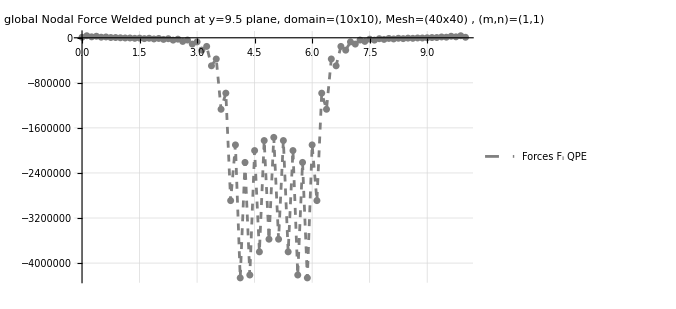

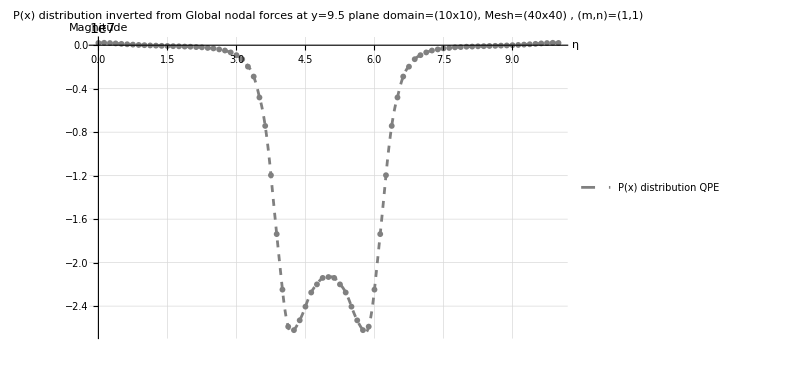

```mathematica
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=40; (*For*)
{m1,n1,m2,n2}={1,1,1,1};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 1};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];

(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{All,All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch at y=9.5 plane, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]

(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.007]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE]
```

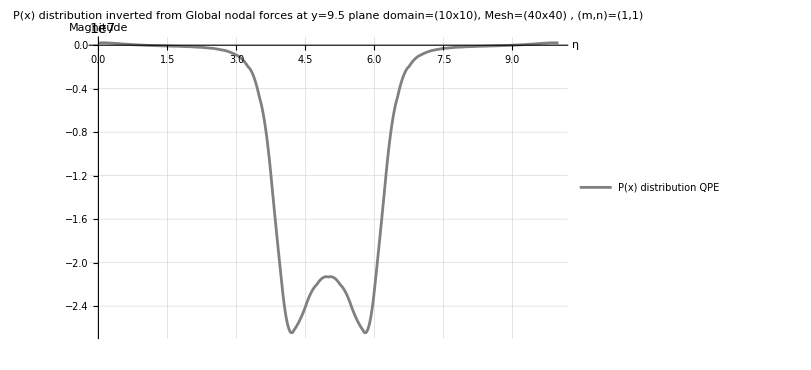

```mathematica
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
```

#### p(x) y=5. Frictionless punch_Geom 10x10, 40x40 mesh (m1,n1,m2,n2;ngauss)(1,1,1,1;3)

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[1;;81]];
xcoordglobal=underpunchdata[[All,2]];
Fy={-105881.3411528049,-447801.9686063286,-236550.385156109,-500585.01747212745,-264432.7155972505,-558803.3202806488,-294682.8260809779,-621197.2281388305,-326763.71222642995,-686830.0039968118,-360269.49692868255,-754981.7389092259,-394878.73745163716,-825056.0690188892,-430309.6787598431,-896495.1274736784,-466280.2437596489,-968705.6476808358,-502474.4015682796,-1.0409994363215137*^6,-538516.5359400166,-1.1125514283155054*^6,-573955.3792458512,-1.1823782364631593*^6,-608258.8152518049,-1.249339298671078*^6,-640820.2959049665,-1.3121612925013192*^6,-670976.7462206325,-1.369484488615794*^6,-698036.7255029324,-1.4199274040076304*^6,-721316.4434784828,-1.4621638981717508*^6,-740180.2213799413,-1.4950051803914625*^6,-754081.3526405925,-1.5174784172961693*^6,-762599.1865599807,-1.528893892860176*^6,-765468.6441020519,-1.5288938928601947*^6,-762599.1865600105,-1.5174784172962029*^6,-754081.3526406176,-1.495005180391511*^6,-740180.2213799674,-1.4621638981717601*^6,-721316.4434784818,-1.4199274040077236*^6,-698036.7255030032,-1.3694844886158556*^6,-670976.7462206502,-1.3121612925013863*^6,-640820.2959050052,-1.2493392986712102*^6,-608258.8152518757,-1.1823782364632785*^6,-573955.3792459071,-1.1125514283156134*^6,-538516.5359400474,-1.0409994363216031*^6,-502474.4015683364,-968705.6476809625,-466280.24375971593,-896495.1274738368,-430309.67875992134,-825056.0690190513,-394878.7374516912,-754981.7389093358,-360269.49692874216,-686830.0039969962,-326763.7122265268,-621197.2281389628,-294682.82608106546,-558803.3202807959,-264432.71559735946,-500585.0174723156,-236550.38515619002,-447801.96860646084,-105881.34115284123};
```

PxResultant

Nodal traction vectors P(1,1) = {-2.544×10^6,-2.685×10^6,-2.841×10^6,-3.002×10^6,-3.175×10^6,-3.352×10^6,-3.538×10^6,-3.726×10^6,-3.923×10^6,-4.120×10^6,-4.324×10^6,-4.529×10^6,-4.739×10^6,-4.950×10^6,-5.164×10^6,-5.379×10^6,-5.596×10^6,-5.812×10^6,-6.030×10^6,-6.246×10^6,-6.462×10^6,-6.676×10^6,-6.887×10^6,-7.095×10^6,-7.298×10^6,-7.497×10^6,-7.688×10^6,-7.874×10^6,-8.049×10^6,-8.218×10^6,-8.373×10^6,-8.521×10^6,-8.652×10^6,-8.775×10^6,-8.878×10^6,-8.972×10^6,-9.044×10^6,-9.107×10^6,-9.146×10^6,-9.176×10^6,-9.181×10^6,-9.176×10^6,-9.146×10^6,-9.107×10^6,-9.044×10^6,-8.972×10^6,-8.878×10^6,-8.775×10^6,-8.652×10^6,-8.521×10^6,-8.373×10^6,-8.218×10^6,-8.049×10^6,-7.874×10^6,-7.688×10^6,-7.497×10^6,-7.298×10^6,-7.095×10^6,-6.887×10^6,-6.676×10^6,-6.462×10^6,-6.246×10^6,-6.030×10^6,-5.812×10^6,-5.596×10^6,-5.379×10^6,-5.164×10^6,-4.950×10^6,-4.739×10^6,-4.529×10^6,-4.324×10^6,-4.120×10^6,-3.923×10^6,-3.726×10^6,-3.538×10^6,-3.352×10^6,-3.175×10^6,-3.002×10^6,-2.841×10^6,-2.685×10^6,-2.544×10^6}

p(x) resultant force P(1,1) = -6.28497×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2026_01_21_analysis element nodal force, traction\2026_01_21_punch_results\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)\NodalTraction.xlsx

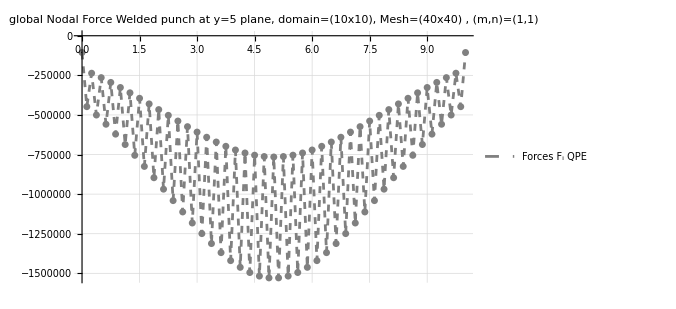

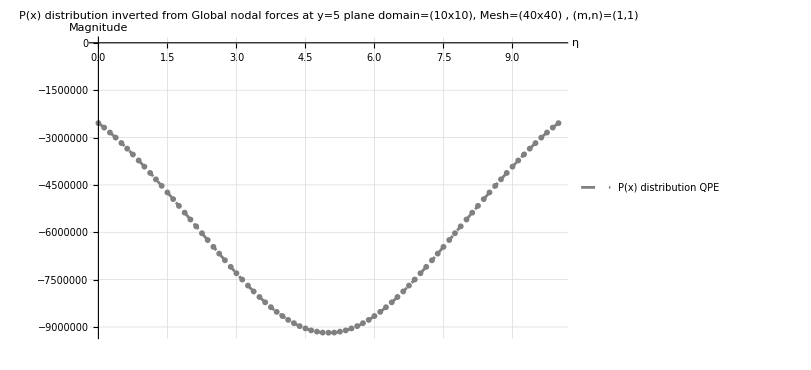

```mathematica
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=40; (*For*)
{m1,n1,m2,n2}={1,1,1,1};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 1};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];

(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{All,All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch at y=5 plane, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]

(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.007]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE]
```

```mathematica
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
```

-Graphics-

#### Traction along horizontal plane y=0.25

```mathematica
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
elenodalforce="ElementForce.xlsx";
elenodalforcedata=Import[FileNameJoin[{dir2,elenodalforce}]];

eleforcedata=Drop[Drop[elenodalforcedata[[1]],{1,1}],{1,1}];
fyrow1=Take[eleforcedata[[All,{9,15,7}]],40];
fxrow1=Take[eleforcedata[[All,{8,14,6}]],40];

Ne=Length[fyrow1];
Fgxrow1=ConstantArray[0,2 Ne+1];
Fgyrow1=ConstantArray[0,2 Ne+1];

Do[
Fgxrow1[[{2 e-1,2 e,2 e+1}]]+=fxrow1[[e]];
Fgyrow1[[{2 e-1,2 e,2 e+1}]]+=fyrow1[[e]];
,{e,1,40}];
```

```mathematica
ListLinePlot[{Fgxrow1,Fgyrow1},PlotRange->All,PlotLegends->Placed[{Style["fx",16],Style["fy",16]},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along top edge of 1st row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

-Graphics-

```mathematica
(*
Comments: 
- fy is symmetric along the mid plane of the domain, which is expected;
 - fx is skew-symmetric along the mid plane of the domain, which is expected;
 - insight about nodal force distribution: for the fy nodal for, at the edge we have high value but does not means the traction is high;
 - There are mixed boundary condition feature at the two outer edge.
*)
```

#### Traction along horizontal plane y=9.25 & 9.75

```mathematica
fxY9=Take[eleforcedata[[All,{8,14,6}]],{1441,1480}];
fyY9=Take[eleforcedata[[All,{9,15,7}]],{1441,1480}];

Ne=Length[fxY9];
FgxY9=ConstantArray[0,2 Ne+1];
FgyY9=ConstantArray[0,2 Ne+1];

Do[
FgxY9[[{2 e-1,2 e,2 e+1}]]+=fxY9[[e]];
FgyY9[[{2 e-1,2 e,2 e+1}]]+=fyY9[[e]];
,{e,1,40}];

fxY95=Take[eleforcedata[[All,{8,14,6}]],{1521,1560}]; (*top edges of second row from the top*)
fyY95=Take[eleforcedata[[All,{9,15,7}]],{1521,1560}]; (*top edge of second row from the top*)

Ne=Length[fxY95];
FgxY95=ConstantArray[0,2 Ne+1];
FgyY95=ConstantArray[0,2 Ne+1];

Do[
FgxY95[[{2 e-1,2 e,2 e+1}]]+=fxY95[[e]];
FgyY95[[{2 e-1,2 e,2 e+1}]]+=fyY95[[e]];
,{e,1,40}];
FgyY95

ListLinePlot[{FgxY9,FgyY9,FgxY95,FgyY95},PlotRange->All,
PlotLegends->Placed[{
Style["fx, y=9",16],Style["fy,  y=9",16],
Style["fx, y=9.5",16],Style["fy,  y=9.5",16]
},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along y=9.5 row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

{874.559,10012.1,5828.84,9433.15,3499.19,5048.85,1548.87,1752.11,262.038,-419.427,-565.498,-1866.08,-1126.57,-2934.77,-1569.47,-3916.55,-2026.15,-5125.65,-2660.65,-7050.54,-3765.95,-10720.3,-6023.82,-18821.4,-11377.1,-39889.2,-26888.2,-109364.,-91501.5,-443217.,-569778.,-2.97312×10^6,-2.71762×10^6,-5.68147×10^6,-2.64125×10^6,-4.40261×10^6,-1.96464×10^6,-3.69016×10^6,-1.75115×10^6,-3.43339×10^6,-1.69414×10^6,-3.43339×10^6,-1.75115×10^6,-3.69016×10^6,-1.96464×10^6,-4.40261×10^6,-2.64125×10^6,-5.68147×10^6,-2.71762×10^6,-2.97312×10^6,-569778.,-443217.,-91501.5,-109364.,-26888.2,-39889.2,-11377.1,-18821.4,-6023.82,-10720.3,-3765.95,-7050.54,-2660.65,-5125.65,-2026.15,-3916.55,-1569.47,-2934.77,-1126.57,-1866.08,-565.498,-419.427,262.038,1752.11,1548.87,5048.85,3499.19,9433.15,5828.84,10012.1,874.559}

-Graphics-

#### Traction along horizontal plane y=9.5

```mathematica
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
elenodalforce="ElementForce.xlsx";
elenodalforcedata=Import[FileNameJoin[{dir2,elenodalforce}]];

eleforcedata=Drop[Drop[elenodalforcedata[[1]],{1,1}],{1,1}];
fxY95=Take[eleforcedata[[All,{8,14,6}]],{1481,1520}]; (*top edges of second row from the top*)
fyY95=Take[eleforcedata[[All,{9,15,7}]],{1481,1520}]; (*top edge of second row from the top*)

Ne=Length[fxY95];
FgxY95=ConstantArray[0,2 Ne+1];
FgyY95=ConstantArray[0,2 Ne+1];

Do[
FgxY95[[{2 e-1,2 e,2 e+1}]]+=fxY95[[e]];
FgyY95[[{2 e-1,2 e,2 e+1}]]+=fyY95[[e]];
,{e,1,40}];
FgyY95

ListLinePlot[{FgxY95,FgyY95},PlotRange->All,
PlotLegends->Placed[{
Style["fx, y=9",16],Style["fy,  y=9",16],
Style["fx, y=9.5",16],Style["fy,  y=9.5",16]
},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along y=9.5 row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

{8931.19,36150.4,16733.,27202.9,10382.,14592.7,4450.08,4149.4,-27.9439,-3645.01,-3345.51,-9656.98,-6026.23,-14965.9,-8621.09,-20764.7,-11776.9,-28657.4,-16466.4,-41394.6,-24520.1,-64667.4,-39986.8,-112022.,-73091.4,-219928.,-153340.,-497534.,-376277.,-1.26927×10^6,-983136.,-2.89096×10^6,-1.90188×10^6,-4.26303×10^6,-2.21277×10^6,-4.2119×10^6,-2.00245×10^6,-3.80064×10^6,-1.82444×10^6,-3.57601×10^6,-1.76848×10^6,-3.57601×10^6,-1.82444×10^6,-3.80064×10^6,-2.00245×10^6,-4.2119×10^6,-2.21277×10^6,-4.26303×10^6,-1.90188×10^6,-2.89096×10^6,-983136.,-1.26927×10^6,-376277.,-497534.,-153340.,-219928.,-73091.4,-112022.,-39986.8,-64667.4,-24520.1,-41394.6,-16466.4,-28657.4,-11776.9,-20764.7,-8621.09,-14965.9,-6026.23,-9656.98,-3345.51,-3645.01,-27.9439,4149.4,4450.08,14592.7,10382.,27202.9,16733.,36150.4,8931.19}

-Graphics-

#### Traction along horizontal plane y=5

```mathematica
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
elenodalforce="ElementForce.xlsx";
elenodalforcedata=Import[FileNameJoin[{dir2,elenodalforce}]];

eleforcedata=Drop[Drop[elenodalforcedata[[1]],{1,1}],{1,1}];
fxY95=Take[eleforcedata[[All,{8,14,6}]],{761,800}]; (*top edges of second row from the top*)
fyY95=Take[eleforcedata[[All,{9,15,7}]],{761,800}]; (*top edge of second row from the top*)

Ne=Length[fxY95];
FgxY95=ConstantArray[0,2 Ne+1];
FgyY95=ConstantArray[0,2 Ne+1];

Do[
FgxY95[[{2 e-1,2 e,2 e+1}]]+=fxY95[[e]];
FgyY95[[{2 e-1,2 e,2 e+1}]]+=fyY95[[e]];
,{e,1,40}];
FgyY95

ListLinePlot[{FgxY95,FgyY95},PlotRange->All,
PlotLegends->Placed[{
Style["fx, y=9",16],Style["fy,  y=5",16],
Style["fx, y=9.5",16],Style["fy,  y=5",16]
},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along y=5 row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

{-105881.,-447802.,-236550.,-500585.,-264433.,-558803.,-294683.,-621197.,-326764.,-686830.,-360269.,-754982.,-394879.,-825056.,-430310.,-896495.,-466280.,-968706.,-502474.,-1.041×10^6,-538517.,-1.11255×10^6,-573955.,-1.18238×10^6,-608259.,-1.24934×10^6,-640820.,-1.31216×10^6,-670977.,-1.36948×10^6,-698037.,-1.41993×10^6,-721316.,-1.46216×10^6,-740180.,-1.49501×10^6,-754081.,-1.51748×10^6,-762599.,-1.52889×10^6,-765469.,-1.52889×10^6,-762599.,-1.51748×10^6,-754081.,-1.49501×10^6,-740180.,-1.46216×10^6,-721316.,-1.41993×10^6,-698037.,-1.36948×10^6,-670977.,-1.31216×10^6,-640820.,-1.24934×10^6,-608259.,-1.18238×10^6,-573955.,-1.11255×10^6,-538517.,-1.041×10^6,-502474.,-968706.,-466280.,-896495.,-430310.,-825056.,-394879.,-754982.,-360269.,-686830.,-326764.,-621197.,-294683.,-558803.,-264433.,-500585.,-236550.,-447802.,-105881.}

-Graphics-

#### Functions to invert from nodal force to traction

```mathematica
Clear["Global`*"]
(*Gamma function and its values at zero*)
γ[η_,m_,n_]:=Abs[1-(1-((η+1)/2)^2)^m]^n
γ01[m_,n_]:=γ[0,m,n]
γ02[m_,n_]:=γ[0,m,n]
NAG3one[η_,m_,n_]:=(-γ01[m,n]+(γ01[m,n]-1) η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3two[η_,m_,n_]:=(1+η-2 γ[η,m,n])/(1-2 γ01[m,n])
NAG3three[η_,m_,n_]:=(-γ01[m,n]-γ01[m,n] η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3t2one[η_,m_,n_]:=NAG3three[-η,m,n]
NAG3t2two[η_,m_,n_]:=NAG3two[-η,m,n]
NAG3t2three[η_,m_,n_]:=NAG3one[-η,m,n]
(*Shape function for AG type 1*)
NShape[η_,m_,n_]:={NAG3one[η,m,n],NAG3two[η,m,n],NAG3three[η,m,n]};
dNShape[η_,m_,n_]:=D[NShape[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(*Shape function for AG type 2*)
NShape2[η_,m_,n_]:={NAG3t2one[η,m,n],NAG3t2two[η,m,n],NAG3t2three[η,m,n]};
dNShape2[η_,m_,n_]:=D[NShape2[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(***************************************************************)
(*Function to get the M matrices: relate Nodal force and Nodal traction*)
elementMmatrix[xpos_,AGtype_]:= Module[{},
{m,n,type}={AGtype[[1]],AGtype[[2]],AGtype[[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
(*Print[AGshape[η,m,n]];*)
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
M=Table[NIntegrate[AGshape[η,m,n][[j]]*AGshape[η,m,n][[i]]*jac,{η,-1,1}],{i,1,3},{j,1,3}]
];
(***************************************************************)
(*Function Global M matrices: relate Global Nodal force and Nodal traction*)
GlobalMmat[xcoord_,conns_,AGtype_]:=Module[{n=Max@Flatten@conns,GlobalMat,Me,conn},
GlobalMat=ConstantArray[0.,{n,n}];
Do[
Me=elementMmatrix[xcoord[[e]],AGtype[[e]]];
(*Print[Me//MatrixForm];*)
conn=conns[[e]];
Do[
GlobalMat[[conn[[i]],conn[[j]]]]+=Me[[i,j]],{i,3},{j,3}],
{e,Length@conns}];
GlobalMat  (* <--return M assembled*)
]
(***************************************************************)
(*Function Global M matrices: relate Global Nodal force and Nodal traction*)
PxinterpolatedData[Pvec_,AGtype_,xcoord_]:=Module[{},
Pxdata={};
(*total=0;*)
Pelem=Partition[Pvec,3,2];
nelem= Length[conns];
Do[
elem=e;
{m,n,type}={AGtype[[elem]][[1]],AGtype[[elem]][[2]],AGtype[[elem]][[5]]};
If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
Clear[x,η];
xη=AGshape[η,1,1].xcoord[[elem]];
ηmap=η/.NSolve[xη==x,η]//First;
PinterpolatePhysical=Sum[AGshape[η,m,n][[i]]*Pelem[[elem]][[i]],{i,1,3}]/.{η->ηmap};(*geometric mapping*)
(*resultant=NIntegrate[PinterpolatePhysical,{x,xmin,xmax}];
PxResultant=total+resultant;*)

{xmin,xmax}={Min[xcoord[[elem]]],Max[xcoord[[elem]]]};
n=100;
dx=(xmax-xmin)/n;
xdata=Table[xmin+i dx,{i,0,n}];
pdata=PinterpolatePhysical/.x->xdata;
plotdata=Transpose[{xdata, pdata}];
Pxdata=AppendTo[Pxdata, plotdata];
,{e,1,nelem}];
Print[PxResultant];
Flatten[Pxdata,1]
]


ComputeResultant[Pelem_,xcoord_,AGtype_]:=Module[{},
totalResutant=0;
Do[
elem=e;
xpos=xcoord[[elem]];
{m,n,type}={AGtype[[elem]][[1]],AGtype[[elem]][[2]],AGtype[[elem]][[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];

resultant=Pelem[[elem]].NIntegrate[AGshape[η,m,n]*jac,{η,-1,1}];
(*Print[resultant];*)
totalResutant=totalResutant+resultant;
,{e,1,Length[conns]}];
totalResutant
]
```

#### p(x) y=9.75 Frictionless punch_Geom 10x10, 40x40 mesh (m1,n1,m2,n2;ngauss)(1,1,1,1;3)

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[1;;81]];
xcoordglobal=underpunchdata[[All,2]];
Fy={874.5585379246622,10012.066707469523,5828.837214931846,9433.14819746092,3499.190758327022,5048.849882092327,1548.8654054701328,1752.1068527530879,262.037510111928,-419.4269038606435,-565.4979969430715,-1866.078010732308,-1126.5741941481829,-2934.768232975155,-1569.473992453888,-3916.5542440004647,-2026.1494517568499,-5125.653418134898,-2660.645878314972,-7050.538168698549,-3765.946733383462,-10720.254240475595,-6023.818817406893,-18821.385634176433,-11377.13286681287,-39889.16538722068,-26888.222640741616,-109364.12359185517,-91501.51494437829,-443216.99130116403,-569778.0549563803,-2.9731210739717856*^6,-2.7176165933358185*^6,-5.681472530769251*^6,-2.641249089443933*^6,-4.402614017195217*^6,-1.9646400330669358*^6,-3.6901600986486003*^6,-1.751153557897061*^6,-3.433393641034119*^6,-1.6941394243013598*^6,-3.4333936410341263*^6,-1.7511535578969605*^6,-3.690160098648511*^6,-1.9646400330667794*^6,-4.402614017194971*^6,-2.6412490894435644*^6,-5.681472530768432*^6,-2.7176165933354944*^6,-2.973121073971458*^6,-569778.0549562667,-443216.99130117893,-91501.51494431868,-109364.12359180301,-26888.222640704364,-39889.165387265384,-11377.132866811007,-18821.385634362698,-6023.818817451596,-10720.254240490496,-3765.9467334225774,-7050.538168799132,-2660.6458782963455,-5125.653418153524,-2026.1494517102838,-3916.554243963212,-1569.4739924632013,-2934.768233049661,-1126.5741941416636,-1866.0780108310282,-565.4979969328269,-419.42690392397344,262.0375100951642,1752.106852741912,1548.8654054785147,5048.849882142618,3499.190758343786,9433.14819746837,5828.837214957923,10012.066707458347,874.5585379200056};
```

```mathematica
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=40; (*For*)
{m1,n1,m2,n2}={1,1,1,1};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 1};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];

(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{All,All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch at y=9.5 plane, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]

(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.007]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE]
```

PxResultant

Nodal traction vectors P(1,1) = {8802.876,66165.665,62595.808,57855.863,40546.180,30480.234,18542.938,10368.953,3631.848,-2860.271,-5915.294,-11723.440,-12261.864,-18338.664,-17114.920,-24488.039,-21974.025,-32104.976,-28725.372,-44154.552,-41070.499,-66591.063,-69416.247,-113528.354,-151640.057,-223620.490,-452745.950,-541811.966,-1.775×10^6,-2.097×10^6,-8.042×10^6,-1.720×10^7,-3.277×10^7,-3.457×10^7,-3.156×10^7,-2.607×10^7,-2.404×10^7,-2.202×10^7,-2.118×10^7,-2.055×10^7,-2.043×10^7,-2.055×10^7,-2.118×10^7,-2.202×10^7,-2.404×10^7,-2.607×10^7,-3.156×10^7,-3.457×10^7,-3.277×10^7,-1.720×10^7,-8.042×10^6,-2.097×10^6,-1.775×10^6,-541811.966,-452745.950,-223620.490,-151640.057,-113528.354,-69416.247,-66591.063,-41070.499,-44154.552,-28725.372,-32104.976,-21974.025,-24488.039,-17114.920,-18338.664,-12261.864,-11723.440,-5915.294,-2860.271,3631.848,10368.953,18542.938,30480.234,40546.180,57855.863,62595.808,66165.665,8802.876}

p(x) resultant force P(1,1) = -6.28497×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2026_01_21_analysis element nodal force, traction\2026_01_21_punch_results\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)\NodalTraction.xlsx

-Graphics-

-Graphics-

```mathematica
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
```

-Graphics-

#### p(x) y=9.5 Frictionless punch_Geom 10x10, 40x40 mesh (m1,n1,m2,n2;ngauss)(1,1,1,1;3)

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[1;;81]];
xcoordglobal=underpunchdata[[All,2]];
Fy={8931.194194601849,36150.387278262526,16732.993409309536,27202.933679083362,10381.975375056267,14592.732172805816,4450.079402578995,4149.396912202239,-27.94385534338653,-3645.007299689576,-3345.510621391237,-9656.982449194416,-6026.228433556855,-14965.903125721961,-8621.08869804442,-20764.664911091328,-11776.861477453262,-28657.36374413222,-16466.397777818143,-41394.615812167525,-24520.09788416885,-64667.440345000476,-39986.75515749678,-112021.6798434928,-73091.39986522123,-219928.49225667492,-153340.09677758627,-497534.0016511269,-376276.7581142727,-1.2692700558359697*^6,-983136.1091124676,-2.890955975348592*^6,-1.90188406903857*^6,-4.263028403577238*^6,-2.212771439910911*^6,-4.21189800033918*^6,-2.0024462205932736*^6,-3.8006359167495966*^6,-1.8244359157051556*^6,-3.576010580680676*^6,-1.7684847469690442*^6,-3.5760105806806684*^6,-1.8244359157050252*^6,-3.800635916749522*^6,-2.0024462205930986*^6,-4.211898000338897*^6,-2.2127714399107993*^6,-4.263028403576903*^6,-1.9018840690387934*^6,-2.8909559753483757*^6,-983136.1091124509,-1.2692700558359437*^6,-376276.75811426155,-497534.00165107474,-153340.09677760117,-219928.49225670844,-73091.39986521564,-112021.67984357476,-39986.755157541484,-64667.440345175564,-24520.097884200513,-41394.6158121489,-16466.397777814418,-28657.36374410987,-11776.861477475613,-20764.664911024272,-8621.088698040694,-14965.903125774115,-6026.228433559649,-9656.982449114323,-3345.510621362366,-3645.0072996914387,-27.943855308927596,4149.396912200376,4450.079402573407,14592.732172846794,10381.975375075825,27202.933679126203,16732.993409316987,36150.38727821596,8931.194194590673};
```

```mathematica
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=40; (*For*)
{m1,n1,m2,n2}={1,1,1,1};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 1};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];

(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{All,All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch at y=9.5 plane, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]

(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.007]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE]
```

PxResultant

Nodal traction vectors P(1,1) = {206587.686,220782.811,196173.062,163959.973,124323.171,87074.555,54644.320,24134.852,1240.678,-22684.518,-38464.968,-58808.579,-70485.344,-90758.131,-101403.796,-125674.546,-139079.731,-173100.233,-195560.231,-249248.187,-294131.223,-387234.102,-488042.383,-664699.298,-915664.022,-1.288×10^6,-1.973×10^6,-2.884×10^6,-4.809×10^6,-7.424×10^6,-1.196×10^7,-1.738×10^7,-2.248×10^7,-2.589×10^7,-2.621×10^7,-2.531×10^7,-2.405×10^7,-2.275×10^7,-2.200×10^7,-2.140×10^7,-2.133×10^7,-2.140×10^7,-2.200×10^7,-2.275×10^7,-2.405×10^7,-2.531×10^7,-2.621×10^7,-2.589×10^7,-2.248×10^7,-1.738×10^7,-1.196×10^7,-7.424×10^6,-4.809×10^6,-2.884×10^6,-1.973×10^6,-1.288×10^6,-915664.022,-664699.298,-488042.383,-387234.102,-294131.223,-249248.187,-195560.231,-173100.233,-139079.731,-125674.546,-101403.796,-90758.131,-70485.344,-58808.579,-38464.968,-22684.518,1240.678,24134.852,54644.320,87074.555,124323.171,163959.973,196173.062,220782.811,206587.686}

p(x) resultant force P(1,1) = -6.28497×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2026_01_21_analysis element nodal force, traction\2026_01_21_punch_results\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)\NodalTraction.xlsx

-Graphics-

-Graphics-

```mathematica
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
```

-Graphics-

#### p(x) y=5. Frictionless punch_Geom 10x10, 40x40 mesh (m1,n1,m2,n2;ngauss)(1,1,1,1;3)

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[1;;81]];
xcoordglobal=underpunchdata[[All,2]];
Fy={-105881.3411528049,-447801.9686063286,-236550.385156109,-500585.01747212745,-264432.7155972505,-558803.3202806488,-294682.8260809779,-621197.2281388305,-326763.71222642995,-686830.0039968118,-360269.49692868255,-754981.7389092259,-394878.73745163716,-825056.0690188892,-430309.6787598431,-896495.1274736784,-466280.2437596489,-968705.6476808358,-502474.4015682796,-1.0409994363215137*^6,-538516.5359400166,-1.1125514283155054*^6,-573955.3792458512,-1.1823782364631593*^6,-608258.8152518049,-1.249339298671078*^6,-640820.2959049665,-1.3121612925013192*^6,-670976.7462206325,-1.369484488615794*^6,-698036.7255029324,-1.4199274040076304*^6,-721316.4434784828,-1.4621638981717508*^6,-740180.2213799413,-1.4950051803914625*^6,-754081.3526405925,-1.5174784172961693*^6,-762599.1865599807,-1.528893892860176*^6,-765468.6441020519,-1.5288938928601947*^6,-762599.1865600105,-1.5174784172962029*^6,-754081.3526406176,-1.495005180391511*^6,-740180.2213799674,-1.4621638981717601*^6,-721316.4434784818,-1.4199274040077236*^6,-698036.7255030032,-1.3694844886158556*^6,-670976.7462206502,-1.3121612925013863*^6,-640820.2959050052,-1.2493392986712102*^6,-608258.8152518757,-1.1823782364632785*^6,-573955.3792459071,-1.1125514283156134*^6,-538516.5359400474,-1.0409994363216031*^6,-502474.4015683364,-968705.6476809625,-466280.24375971593,-896495.1274738368,-430309.67875992134,-825056.0690190513,-394878.7374516912,-754981.7389093358,-360269.49692874216,-686830.0039969962,-326763.7122265268,-621197.2281389628,-294682.82608106546,-558803.3202807959,-264432.71559735946,-500585.0174723156,-236550.38515619002,-447801.96860646084,-105881.34115284123};


Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=40; (*For*)
{m1,n1,m2,n2}={1,1,1,1};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 1};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];

(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{All,All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch at y=5 plane, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]

(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.007]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE]
```

PxResultant

Nodal traction vectors P(1,1) = {-2.544×10^6,-2.685×10^6,-2.841×10^6,-3.002×10^6,-3.175×10^6,-3.352×10^6,-3.538×10^6,-3.726×10^6,-3.923×10^6,-4.120×10^6,-4.324×10^6,-4.529×10^6,-4.739×10^6,-4.950×10^6,-5.164×10^6,-5.379×10^6,-5.596×10^6,-5.812×10^6,-6.030×10^6,-6.246×10^6,-6.462×10^6,-6.676×10^6,-6.887×10^6,-7.095×10^6,-7.298×10^6,-7.497×10^6,-7.688×10^6,-7.874×10^6,-8.049×10^6,-8.218×10^6,-8.373×10^6,-8.521×10^6,-8.652×10^6,-8.775×10^6,-8.878×10^6,-8.972×10^6,-9.044×10^6,-9.107×10^6,-9.146×10^6,-9.176×10^6,-9.181×10^6,-9.176×10^6,-9.146×10^6,-9.107×10^6,-9.044×10^6,-8.972×10^6,-8.878×10^6,-8.775×10^6,-8.652×10^6,-8.521×10^6,-8.373×10^6,-8.218×10^6,-8.049×10^6,-7.874×10^6,-7.688×10^6,-7.497×10^6,-7.298×10^6,-7.095×10^6,-6.887×10^6,-6.676×10^6,-6.462×10^6,-6.246×10^6,-6.030×10^6,-5.812×10^6,-5.596×10^6,-5.379×10^6,-5.164×10^6,-4.950×10^6,-4.739×10^6,-4.529×10^6,-4.324×10^6,-4.120×10^6,-3.923×10^6,-3.726×10^6,-3.538×10^6,-3.352×10^6,-3.175×10^6,-3.002×10^6,-2.841×10^6,-2.685×10^6,-2.544×10^6}

p(x) resultant force P(1,1) = -6.28497×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2026_01_21_analysis element nodal force, traction\2026_01_21_punch_results\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)\NodalTraction.xlsx

-Graphics-

-Graphics-

```mathematica
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
```

-Graphics-

### p(x) y=10 Frictionless punch_Geom 10x10, 40x40 mesh (m1,n1,m2,n2;ngauss)(1,1,1,1;3)

#### Traction along horizontal plane y=10

1600

{1599.,1630.52,1618.19,18.5829,-874.559,-4.19095×10^-9,4.65661×10^-9,-867.635,15.3541,9244.44,-10012.1,-1.86265×10^-9,1.49012×10^-8,-1.86265×10^-9,-1.67638×10^-8,-10025.9,9253.08,7.45058×10^-9,2.6077×10^-8}

{-2.79397×10^-9,-7.45058×10^-9,1.39698×10^-8,1.49012×10^-8,1.02445×10^-8,2.04891×10^-8,-5.58794×10^-9,3.72529×10^-9,-1.11759×10^-8,7.45058×10^-9,1.86265×10^-9,-1.86265×10^-8,3.72529×10^-9,9.31323×10^-9,-7.45058×10^-9,2.23517×10^-8,1.11759×10^-8,1.86265×10^-8,7.45058×10^-9,-2.6077×10^-8,-3.1665×10^-8,2.6077×10^-8,2.79397×10^-8,1.11759×10^-8,1.30385×10^-8,-4.84288×10^-8,2.23517×10^-8,1.86265×10^-8,2.23517×10^-8,-4.84288×10^-8,-8.19564×10^-8,1.49012×10^-8,-7.22401×10^6,-6.46522×10^6,-2.23853×10^6,-4.18776×10^6,-1.87016×10^6,-3.56649×10^6,-1.69993×10^6,-3.34658×10^6,-1.65233×10^6,-3.34658×10^6,-1.69993×10^6,-3.56649×10^6,-1.87016×10^6,-4.18776×10^6,-2.23853×10^6,-6.46522×10^6,-7.22401×10^6,5.21541×10^-8,2.04891×10^-8,2.23517×10^-8,-3.72529×10^-9,-1.49012×10^-8,-1.86265×10^-9,1.49012×10^-8,0.,0.,-2.79397×10^-8,1.11759×10^-8,-7.45058×10^-9,1.11759×10^-8,-1.86265×10^-9,-3.72529×10^-9,-7.45058×10^-9,-7.45058×10^-9,6.51926×10^-9,1.11759×10^-8,3.72529×10^-9,2.23517×10^-8,-2.79397×10^-9,1.30385×10^-8,-1.86265×10^-9,-7.45058×10^-9,-7.45058×10^-9,-1.86265×10^-9,-3.72529×10^-9,-7.45058×10^-9,9.31323×10^-10,-1.67638×10^-8,4.65661×10^-9}

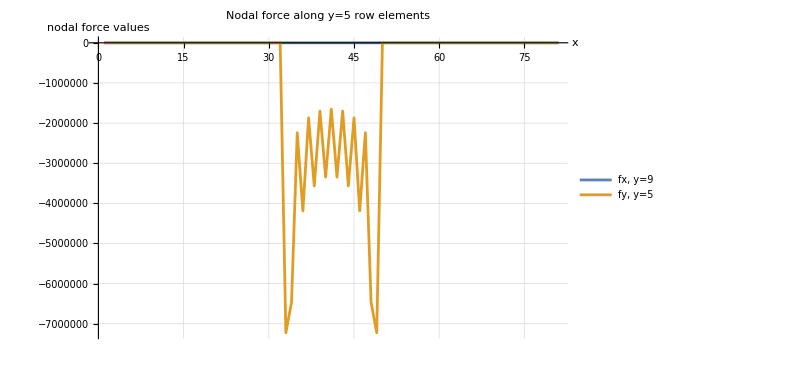

```mathematica
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
elenodalforce="ElementForce.xlsx";
elenodalforcedata=Import[FileNameJoin[{dir2,elenodalforce}]];

eleforcedata=Drop[Drop[elenodalforcedata[[1]],{1,1}],{1,1}]
fxY95=Take[eleforcedata[[All,{8,14,6}]],{1561,1600}]; (*top edges of second row from the top*)
fyY95=Take[eleforcedata[[All,{9,15,7}]],{1561,1600}]; (*top edge of second row from the top*)

Length[eleforcedata]
eleforcedata[[1600]]

Ne=Length[fxY95];
FgxY95=ConstantArray[0,2 Ne+1];
FgyY95=ConstantArray[0,2 Ne+1];

Do[
FgxY95[[{2 e-1,2 e,2 e+1}]]+=fxY95[[e]];
FgyY95[[{2 e-1,2 e,2 e+1}]]+=fyY95[[e]];
,{e,1,40}];
FgyY95

ListLinePlot[{FgxY95,FgyY95},PlotRange->All,
PlotLegends->Placed[{
Style["fx, y=9",16],Style["fy,  y=5",16],
Style["fx, y=9.5",16],Style["fy,  y=5",16]
},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along y=5 row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

#### p(x) y=10

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)";
filename="nodal_displacement_disp_control_(1,1).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[1;;81]];
xcoordglobal=underpunchdata[[All,2]];
Fy={-2.7939677238464355*^-9,-7.450580596923828*^-9,1.3969838619232178*^-8,1.4901161193847656*^-8,1.0244548320770264*^-8,2.0489096641540527*^-8,-5.587935447692871*^-9,3.725290298461914*^-9,-1.1175870895385742*^-8,7.450580596923828*^-9,1.862645149230957*^-9,-1.862645149230957*^-8,3.725290298461914*^-9,9.313225746154785*^-9,-7.450580596923828*^-9,2.2351741790771484*^-8,1.1175870895385742*^-8,1.862645149230957*^-8,7.450580596923828*^-9,-2.60770320892334*^-8,-3.166496753692627*^-8,2.60770320892334*^-8,2.7939677238464355*^-8,1.1175870895385742*^-8,1.30385160446167*^-8,-4.842877388000488*^-8,2.2351741790771484*^-8,1.862645149230957*^-8,2.2351741790771484*^-8,-4.842877388000488*^-8,-8.195638656616211*^-8,1.4901161193847656*^-8,-7.224012855588455*^6,-6.465216602695674*^6,-2.2385309495858774*^6,-4.187763272232972*^6,-1.8701551223874912*^6,-3.566493360402636*^6,-1.6999268669325449*^6,-3.34657594437401*^6,-1.6523273677065112*^6,-3.3465759443740174*^6,-1.6999268669325784*^6,-3.566493360402666*^6,-1.870155122387413*^6,-4.187763272232704*^6,-2.2385309495855905*^6,-6.465216602694921*^6,-7.22401285558754*^6,5.21540641784668*^-8,2.0489096641540527*^-8,2.2351741790771484*^-8,-3.725290298461914*^-9,-1.4901161193847656*^-8,-1.862645149230957*^-9,1.4901161193847656*^-8,0.,0.,-2.7939677238464355*^-8,1.1175870895385742*^-8,-7.450580596923828*^-9,1.1175870895385742*^-8,-1.862645149230957*^-9,-3.725290298461914*^-9,-7.450580596923828*^-9,-7.450580596923828*^-9,6.51925802230835*^-9,1.1175870895385742*^-8,3.725290298461914*^-9,2.2351741790771484*^-8,-2.7939677238464355*^-9,1.30385160446167*^-8,-1.862645149230957*^-9,-7.450580596923828*^-9,-7.450580596923828*^-9,-1.862645149230957*^-9,-3.725290298461914*^-9,-7.450580596923828*^-9,9.313225746154785*^-10,-1.6763806343078613*^-8,4.6566128730773926*^-9};
```

PxResultant

Nodal traction vectors P(1,1) = {-0.000,0.000,-0.000,0.000,-0.002,0.002,-0.013,0.011,-0.073,0.062,-0.425,0.363,-2.477,2.114,-14.437,12.323,-84.145,71.823,-490.436,418.613,-2858.470,2439.857,-16660.382,14220.526,-97103.825,82883.299,-565962.567,483079.268,-3.299×10^6,2.816×10^6,-1.923×10^7,1.641×10^7,-1.121×10^8,-2.983×10^7,-3.720×10^7,-2.375×10^7,-2.407×10^7,-2.115×10^7,-2.071×10^7,-2.002×10^7,-1.995×10^7,-2.002×10^7,-2.071×10^7,-2.115×10^7,-2.407×10^7,-2.375×10^7,-3.720×10^7,-2.983×10^7,-1.121×10^8,1.641×10^7,-1.923×10^7,2.816×10^6,-3.299×10^6,483079.268,-565962.567,82883.299,-97103.825,14220.526,-16660.382,2439.857,-2858.470,418.613,-490.436,71.823,-84.145,12.323,-14.437,2.114,-2.477,0.363,-0.425,0.062,-0.073,0.011,-0.013,0.002,-0.002,0.000,-0.000,0.000,-0.000}

p(x) resultant force P(1,1) = -6.28497×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2026_01_21_analysis element nodal force, traction\2026_01_21_punch_results\Frictionless_dz=-0.1_disp_control(40,40)_rigid_punch_(1,1,1,1,10)\NodalTraction.xlsx

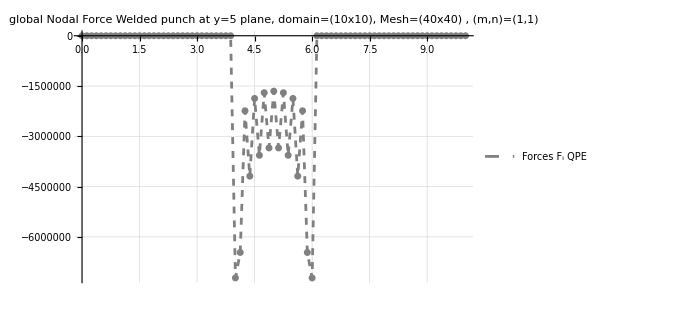

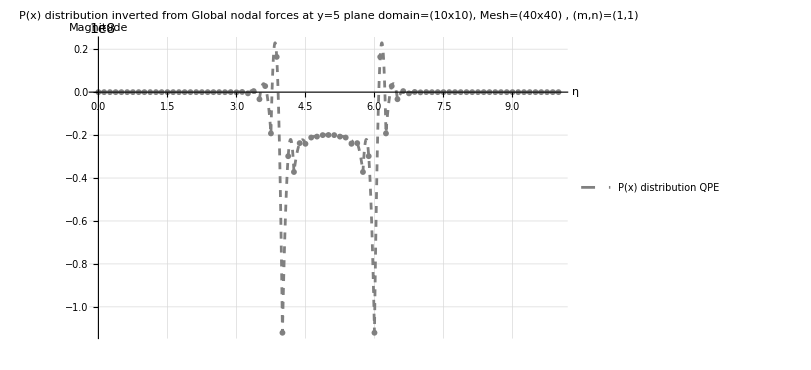

```mathematica
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=40; (*For*)
{m1,n1,m2,n2}={1,1,1,1};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[1]]={m1,n1,m2,n2, 1};
AGtype[[-1]]={m1,n1,m2,n2, 1};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];

(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{All,All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch at y=5 plane, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]

(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.007]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE]
```

```mathematica
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
```

-Graphics-

### p(x) y=10 Frictionless punch_Geom 10x10, 40x40 mesh (m1,n1,m2,n2;ngauss)(1,10,1,10;3)

#### Functions to invert from nodal force to traction

```mathematica
Clear["Global`*"]
(*Gamma function and its values at zero*)
γ[η_,m_,n_]:=Abs[1-(1-((η+1)/2)^2)^m]^n
γ01[m_,n_]:=γ[0,m,n]
γ02[m_,n_]:=γ[0,m,n]
NAG3one[η_,m_,n_]:=(-γ01[m,n]+(γ01[m,n]-1) η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3two[η_,m_,n_]:=(1+η-2 γ[η,m,n])/(1-2 γ01[m,n])
NAG3three[η_,m_,n_]:=(-γ01[m,n]-γ01[m,n] η+γ[η,m,n])/(1-2 γ01[m,n])
NAG3t2one[η_,m_,n_]:=NAG3three[-η,m,n]
NAG3t2two[η_,m_,n_]:=NAG3two[-η,m,n]
NAG3t2three[η_,m_,n_]:=NAG3one[-η,m,n]
(*Shape function for AG type 1*)
NShape[η_,m_,n_]:={NAG3one[η,m,n],NAG3two[η,m,n],NAG3three[η,m,n]};
dNShape[η_,m_,n_]:=D[NShape[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(*Shape function for AG type 2*)
NShape2[η_,m_,n_]:={NAG3t2one[η,m,n],NAG3t2two[η,m,n],NAG3t2three[η,m,n]};
dNShape2[η_,m_,n_]:=D[NShape2[η,m,n],η]/. Derivative[1][Abs][a_]:>Sign[a];
(***************************************************************)
(*Function to get the M matrices: relate Nodal force and Nodal traction*)
elementMmatrix[xpos_,AGtype_]:= Module[{},
{m,n,type}={AGtype[[1]],AGtype[[2]],AGtype[[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
(*Print[AGshape[η,m,n]];*)
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
M=Table[NIntegrate[AGshape[η,m,n][[j]]*AGshape[η,m,n][[i]]*jac,{η,-1,1}],{i,1,3},{j,1,3}]
];
(***************************************************************)
(*Function Global M matrices: relate Global Nodal force and Nodal traction*)
GlobalMmat[xcoord_,conns_,AGtype_]:=Module[{n=Max@Flatten@conns,GlobalMat,Me,conn},
GlobalMat=ConstantArray[0.,{n,n}];
Do[
Me=elementMmatrix[xcoord[[e]],AGtype[[e]]];
(*Print[Me//MatrixForm];*)
conn=conns[[e]];
Do[
GlobalMat[[conn[[i]],conn[[j]]]]+=Me[[i,j]],{i,3},{j,3}],
{e,Length@conns}];
GlobalMat  (* <--return M assembled*)
]
(***************************************************************)
(*Function Global M matrices: relate Global Nodal force and Nodal traction*)
PxinterpolatedData[Pvec_,AGtype_,xcoord_]:=Module[{},
Pxdata={};
(*total=0;*)
Pelem=Partition[Pvec,3,2];
nelem= Length[conns];
Do[
elem=e;
{m,n,type}={AGtype[[elem]][[1]],AGtype[[elem]][[2]],AGtype[[elem]][[5]]};
If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
Clear[x,η];
xη=AGshape[η,1,1].xcoord[[elem]];
ηmap=η/.NSolve[xη==x,η]//First;
PinterpolatePhysical=Sum[AGshape[η,m,n][[i]]*Pelem[[elem]][[i]],{i,1,3}]/.{η->ηmap};(*geometric mapping*)
(*resultant=NIntegrate[PinterpolatePhysical,{x,xmin,xmax}];
PxResultant=total+resultant;*)

{xmin,xmax}={Min[xcoord[[elem]]],Max[xcoord[[elem]]]};
n=100;
dx=(xmax-xmin)/n;
xdata=Table[xmin+i dx,{i,0,n}];
pdata=PinterpolatePhysical/.x->xdata;
plotdata=Transpose[{xdata, pdata}];
Pxdata=AppendTo[Pxdata, plotdata];
,{e,1,nelem}];
Print[PxResultant];
Flatten[Pxdata,1]
]


ComputeResultant[Pelem_,xcoord_,AGtype_]:=Module[{},
totalResutant=0;
Do[
elem=e;
xpos=xcoord[[elem]];
{m,n,type}={AGtype[[elem]][[1]],AGtype[[elem]][[2]],AGtype[[elem]][[5]]};

If[type==1,
{AGshape[η_,m_,n_]:=NShape[η,m,n],dAGshape[η_,m_,n_]:=dNShape[η,m,n]},
{AGshape[η_,m_,n_]:=NShape2[η,m,n],dAGshape[η_,m_,n_]:=dNShape2[η,m,n]}
];
x=Sum[AGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];
jac=Sum[dAGshape[η,1,1][[i]]*xpos[[i]],{i,1,3}];

resultant=Pelem[[elem]].NIntegrate[AGshape[η,m,n]*jac,{η,-1,1}];
(*Print[resultant];*)
totalResutant=totalResutant+resultant;
,{e,1,Length[conns]}];
totalResutant
]
```

#### Element force v2 (with element_id as input)

```mathematica
Clear["Global`*"]
```

```mathematica
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
estifffile="Ke_by_element.xlsx";
connfile="connectivity_Q9_40x40.xlsx";
dispfile="nodal_displacement_disp_control_(1,10).xlsx";

estiffdata=Import[FileNameJoin[{dir,estifffile}]];
conndata=Import[FileNameJoin[{dir2,connfile}]];
dispdata=Import[FileNameJoin[{dir2,dispfile}]];
(*connectivity without headers (same idea as your earlier snippet)*)
connmatrix=Drop[Drop[conndata[[1]],1],None,1];
(*nodal table without header row*)
nodaldata=Drop[dispdata[[1]],1];
(* =========================Functions=========================*)

ClearAll[estiffness,elemnodeid,nodaldispvec,elemforce];
(*Element stiffness matrix with redundant rows/cols removed*)
estiffness[elemid_Integer]:=Drop[Drop[estiffdata[[elemid+1]],{1,6}],None,{1,1}];
(*Element node IDs (Python 0-based stored in file)*)
elemnodeid[elemid_Integer]:=connmatrix[[elemid+1]];
(*Flattened displacement vector compatible with Ke*)
nodaldispvec[elemid_Integer]:=Module[{elemnode,nodalsol,nodaldisp},elemnode=elemnodeid[elemid];
nodalsol=nodaldata[[elemnode+1]];(*+1 because Mathematica is 1-based*)nodaldisp=nodalsol[[All,{4,5}]];(*columns Ux,Uy*)Flatten[nodaldisp]];
(*Element nodal force vector*)
elemforce[elemid_Integer]:=estiffness[elemid].nodaldispvec[elemid];
```

```mathematica
Ne=Length[connmatrix];  (*number of elements*)

forceMat=Table[Prepend[Flatten@elemforce[e],e],(*add elemid (0-based) as first column*){e,0,Ne-1}];

header18=Flatten@Table[{"f"<>ToString[i]<>"_1","f"<>ToString[i]<>"_2"},{i,1,9}];

header19=Prepend[header18,"elemid(py0)"];

Export[FileNameJoin[{dir2,"ElementForce.xlsx"}],Prepend[forceMat,header19],"XLSX"];
```

#### Traction along horizontal plane y=10

{1.86265×10^-9,1.30385×10^-8,1.49012×10^-8,5.58794×10^-9,-9.31323×10^-9,2.79397×10^-8,-3.72529×10^-9,5.58794×10^-9,-3.72529×10^-9,3.72529×10^-9,9.31323×10^-9,-2.42144×10^-8,-3.72529×10^-9,-3.35276×10^-8,1.86265×10^-9,-2.6077×10^-8,1.49012×10^-8,-2.98023×10^-8,1.49012×10^-8,-4.09782×10^-8,1.86265×10^-8,-1.49012×10^-8,-2.79397×10^-8,1.49012×10^-8,2.79397×10^-8,-2.23517×10^-8,1.11759×10^-8,2.23517×10^-8,-5.58794×10^-8,-7.07805×10^-8,-1.71363×10^-7,4.76837×10^-7,-3.34069×10^6,-1.37205×10^7,1.16778×10^6,-4.18072×10^6,-1.87877×10^6,-3.57105×10^6,-1.70147×10^6,-3.34889×10^6,-1.65342×10^6,-3.34889×10^6,-1.70147×10^6,-3.57105×10^6,-1.87877×10^6,-4.18072×10^6,1.16778×10^6,-1.37205×10^7,-3.34069×10^6,3.12924×10^-7,4.28408×10^-8,-2.98023×10^-8,-7.45058×10^-9,-2.98023×10^-8,-2.98023×10^-8,1.11759×10^-8,-1.30385×10^-8,-1.49012×10^-8,9.31323×10^-10,2.23517×10^-8,2.79397×10^-9,5.58794×10^-8,1.86265×10^-8,-3.35276×10^-8,-1.86265×10^-8,-4.09782×10^-8,9.31323×10^-10,3.35276×10^-8,2.14204×10^-8,-3.72529×10^-9,-3.72529×10^-9,3.53903×10^-8,-9.31323×10^-10,-1.11759×10^-8,-1.86265×10^-9,0.,-2.32831×10^-9,-1.11759×10^-8,3.25963×10^-9,-1.67638×10^-8,3.72529×10^-9}

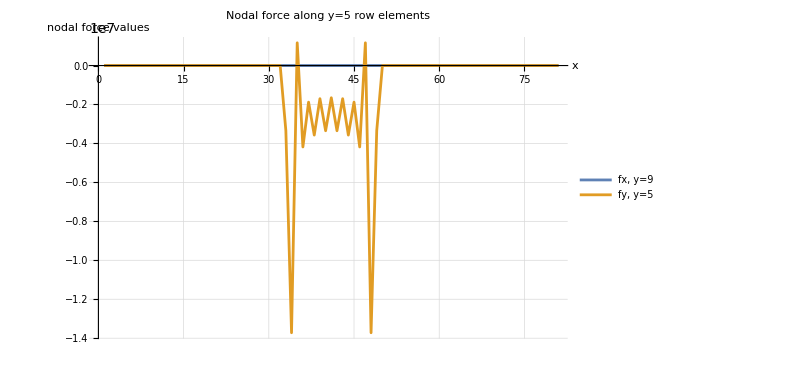

```mathematica
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
elenodalforce="ElementForce.xlsx";
elenodalforcedata=Import[FileNameJoin[{dir2,elenodalforce}]];

eleforcedata=Drop[Drop[elenodalforcedata[[1]],{1,0}],{1,1}];
fxY95=Take[eleforcedata[[All,{8,14,6}]],{1561,1600}];(*top edges of second row from the top*)
fyY95=Take[eleforcedata[[All,{9,15,7}]],{1561,1600}]; (*top edge of second row from the top*)

(*Length[eleforcedata]
eleforcedata[[1600]]*)

Ne=Length[fxY95];
FgxY95=ConstantArray[0,2 Ne+1];
FgyY95=ConstantArray[0,2 Ne+1];

Do[
FgxY95[[{2 e-1,2 e,2 e+1}]]+=fxY95[[e]];
FgyY95[[{2 e-1,2 e,2 e+1}]]+=fyY95[[e]];
,{e,1,40}];
FgyY95

ListLinePlot[{FgxY95,FgyY95},PlotRange->All,
PlotLegends->Placed[{
Style["fx, y=9",16],Style["fy,  y=5",16],
Style["fx, y=9.5",16],Style["fy,  y=5",16]
},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along y=5 row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

#### p(x) y=10

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,10).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[1;;81]];
xcoordglobal=underpunchdata[[All,2]];
Fy={1.862645149230957*^-9,1.30385160446167*^-8,1.4901161193847656*^-8,5.587935447692871*^-9,-9.313225746154785*^-9,2.7939677238464355*^-8,-3.725290298461914*^-9,5.587935447692871*^-9,-3.725290298461914*^-9,3.725290298461914*^-9,9.313225746154785*^-9,-2.421438694000244*^-8,-3.725290298461914*^-9,-3.3527612686157227*^-8,1.862645149230957*^-9,-2.60770320892334*^-8,1.4901161193847656*^-8,-2.9802322387695312*^-8,1.4901161193847656*^-8,-4.0978193283081055*^-8,1.862645149230957*^-8,-1.4901161193847656*^-8,-2.7939677238464355*^-8,1.4901161193847656*^-8,2.7939677238464355*^-8,-2.2351741790771484*^-8,1.1175870895385742*^-8,2.2351741790771484*^-8,-5.587935447692871*^-8,-7.078051567077637*^-8,-1.7136335372924805*^-7,4.76837158203125*^-7,-3.3406874120641374*^6,-1.3720538159021407*^7,1.1677831494912207*^6,-4.1807227586771473*^6,-1.8787691262655072*^6,-3.5710460089880303*^6,-1.7014654550796226*^6,-3.348885755402416*^6,-1.653415688473288*^6,-3.3488857554023117*^6,-1.7014654550795443*^6,-3.571046008988023*^6,-1.8787691262653992*^6,-4.1807227586767375*^6,1.1677831494914442*^6,-1.3720538159018919*^7,-3.3406874120642543*^6,3.129243850708008*^-7,4.284083843231201*^-8,-2.9802322387695312*^-8,-7.450580596923828*^-9,-2.9802322387695312*^-8,-2.9802322387695312*^-8,1.1175870895385742*^-8,-1.30385160446167*^-8,-1.4901161193847656*^-8,9.313225746154785*^-10,2.2351741790771484*^-8,2.7939677238464355*^-9,5.587935447692871*^-8,1.862645149230957*^-8,-3.3527612686157227*^-8,-1.862645149230957*^-8,-4.0978193283081055*^-8,9.313225746154785*^-10,3.3527612686157227*^-8,2.1420419216156006*^-8,-3.725290298461914*^-9,-3.725290298461914*^-9,3.5390257835388184*^-8,-9.313225746154785*^-10,-1.1175870895385742*^-8,-1.862645149230957*^-9,0.,-2.3283064365386963*^-9,-1.1175870895385742*^-8,3.259629011154175*^-9,-1.6763806343078613*^-8,3.725290298461914*^-9};
```

PxResultant

Nodal traction vectors P(1,1) = {-0.000,0.000,-0.000,0.000,-0.001,0.001,-0.005,0.004,-0.030,0.025,-0.173,0.148,-1.009,0.861,-5.881,5.020,-34.278,29.258,-199.787,170.529,-1164.445,993.916,-6786.881,5792.965,-39556.843,33763.877,-230554.174,196790.297,-1.344×10^6,1.147×10^6,-7.832×10^6,8.490×10^6,-2.531×10^8,-4.540×10^7,-2.071×10^7,-2.609×10^7,-2.138×10^7,-2.158×10^7,-2.025×10^7,-2.011×10^7,-1.981×10^7,-2.011×10^7,-2.025×10^7,-2.158×10^7,-2.138×10^7,-2.609×10^7,-2.071×10^7,-4.540×10^7,-2.531×10^8,8.490×10^6,-7.832×10^6,1.147×10^6,-1.344×10^6,196790.297,-230554.174,33763.877,-39556.843,5792.965,-6786.881,993.916,-1164.445,170.529,-199.787,29.258,-34.278,5.020,-5.881,0.861,-1.009,0.148,-0.173,0.025,-0.030,0.004,-0.005,0.001,-0.001,0.000,-0.000,0.000,-0.000}

p(x) resultant force P(1,1) = -6.28021×10^7

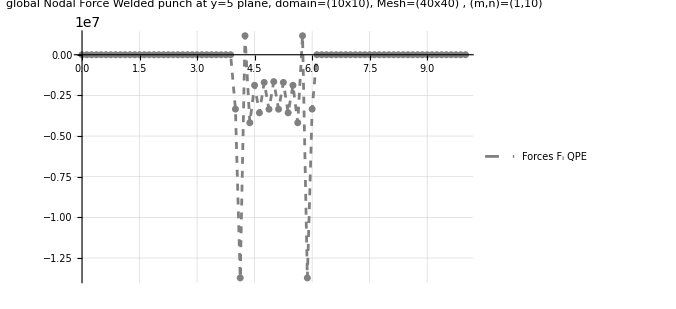

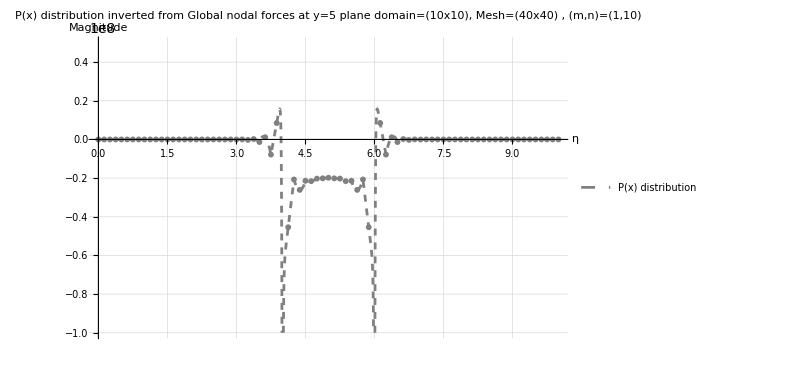

```mathematica
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=40; (*For*)
{m1,n1,m2,n2}={1,10,1,10};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[16]]={m1,n1,m2,n2, 1};
AGtype[[17]]={m1,n1,m2,n2, 2};

AGtype[[24]]={m1,n1,m2,n2, 1};
AGtype[[25]]={m1,n1,m2,n2, 2};


q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];

(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];   (*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
(*Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]*)

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{All,All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch at y=5 plane, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]

(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,{-1*10^8,5*10^7}},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.007]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE]
```

### p(x) y=10 Frictionless punch_Geom 10x10, 40x40 mesh (m1,n1,m2,n2;ngauss)(1,10,1,10;3)_not splitting

#### Element force v2 (with element_id as input)

```mathematica
Clear["Global`*"]
```

```mathematica
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
estifffile="Ke_by_element.xlsx";
connfile="connectivity_Q9_40x40.xlsx";
dispfile="nodal_displacement_disp_control_(1,10).xlsx";

estiffdata=Import[FileNameJoin[{dir,estifffile}]];
conndata=Import[FileNameJoin[{dir2,connfile}]];
dispdata=Import[FileNameJoin[{dir2,dispfile}]];
(*connectivity without headers (same idea as your earlier snippet)*)
connmatrix=Drop[Drop[conndata[[1]],1],None,1];
(*nodal table without header row*)
nodaldata=Drop[dispdata[[1]],1];
(* =========================Functions=========================*)

ClearAll[estiffness,elemnodeid,nodaldispvec,elemforce];
(*Element stiffness matrix with redundant rows/cols removed*)
estiffness[elemid_Integer]:=Drop[Drop[estiffdata[[elemid+1]],{1,6}],None,{1,1}];
(*Element node IDs (Python 0-based stored in file)*)
elemnodeid[elemid_Integer]:=connmatrix[[elemid+1]];
(*Flattened displacement vector compatible with Ke*)
nodaldispvec[elemid_Integer]:=Module[{elemnode,nodalsol,nodaldisp},elemnode=elemnodeid[elemid];
nodalsol=nodaldata[[elemnode+1]];(*+1 because Mathematica is 1-based*)nodaldisp=nodalsol[[All,{4,5}]];(*columns Ux,Uy*)Flatten[nodaldisp]];
(*Element nodal force vector*)
elemforce[elemid_Integer]:=estiffness[elemid].nodaldispvec[elemid];
```

```mathematica
Ne=Length[connmatrix];  (*number of elements*)

forceMat=Table[Prepend[Flatten@elemforce[e],e],(*add elemid (0-based) as first column*){e,0,Ne-1}];

header18=Flatten@Table[{"f"<>ToString[i]<>"_1","f"<>ToString[i]<>"_2"},{i,1,9}];

header19=Prepend[header18,"elemid(py0)"];

Export[FileNameJoin[{dir2,"ElementForce.xlsx"}],Prepend[forceMat,header19],"XLSX"];
```

#### Traction along horizontal plane y=10

```mathematica
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
elenodalforce="ElementForce.xlsx";
elenodalforcedata=Import[FileNameJoin[{dir2,elenodalforce}]];

eleforcedata=Drop[Drop[elenodalforcedata[[1]],{1,0}],{1,1}];
fxY95=Take[eleforcedata[[All,{8,14,6}]],{1561,1600}];(*top edges of second row from the top*)
fyY95=Take[eleforcedata[[All,{9,15,7}]],{1561,1600}]; (*top edge of second row from the top*)

(*Length[eleforcedata]
eleforcedata[[1600]]*)

Ne=Length[fxY95];
FgxY95=ConstantArray[0,2 Ne+1];
FgyY95=ConstantArray[0,2 Ne+1];

Do[
FgxY95[[{2 e-1,2 e,2 e+1}]]+=fxY95[[e]];
FgyY95[[{2 e-1,2 e,2 e+1}]]+=fyY95[[e]];
,{e,1,40}];
FgyY95

ListLinePlot[{FgxY95,FgyY95},PlotRange->All,
PlotLegends->Placed[{
Style["fx, y=9",16],Style["fy,  y=5",16],
Style["fx, y=9.5",16],Style["fy,  y=5",16]
},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along y=5 row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

{1.86265×10^-9,1.30385×10^-8,1.49012×10^-8,5.58794×10^-9,-9.31323×10^-9,2.79397×10^-8,-3.72529×10^-9,5.58794×10^-9,-3.72529×10^-9,3.72529×10^-9,9.31323×10^-9,-2.42144×10^-8,-3.72529×10^-9,-3.35276×10^-8,1.86265×10^-9,-2.6077×10^-8,1.49012×10^-8,-2.98023×10^-8,1.49012×10^-8,-4.09782×10^-8,1.86265×10^-8,-1.49012×10^-8,-2.79397×10^-8,1.49012×10^-8,2.79397×10^-8,-2.23517×10^-8,1.11759×10^-8,2.23517×10^-8,-5.58794×10^-8,-7.07805×10^-8,-1.71363×10^-7,4.76837×10^-7,-3.34069×10^6,-1.37205×10^7,1.16778×10^6,-4.18072×10^6,-1.87877×10^6,-3.57105×10^6,-1.70147×10^6,-3.34889×10^6,-1.65342×10^6,-3.34889×10^6,-1.70147×10^6,-3.57105×10^6,-1.87877×10^6,-4.18072×10^6,1.16778×10^6,-1.37205×10^7,-3.34069×10^6,3.12924×10^-7,4.28408×10^-8,-2.98023×10^-8,-7.45058×10^-9,-2.98023×10^-8,-2.98023×10^-8,1.11759×10^-8,-1.30385×10^-8,-1.49012×10^-8,9.31323×10^-10,2.23517×10^-8,2.79397×10^-9,5.58794×10^-8,1.86265×10^-8,-3.35276×10^-8,-1.86265×10^-8,-4.09782×10^-8,9.31323×10^-10,3.35276×10^-8,2.14204×10^-8,-3.72529×10^-9,-3.72529×10^-9,3.53903×10^-8,-9.31323×10^-10,-1.11759×10^-8,-1.86265×10^-9,0.,-2.32831×10^-9,-1.11759×10^-8,3.25963×10^-9,-1.67638×10^-8,3.72529×10^-9}

-Graphics-

#### p(x) y=10

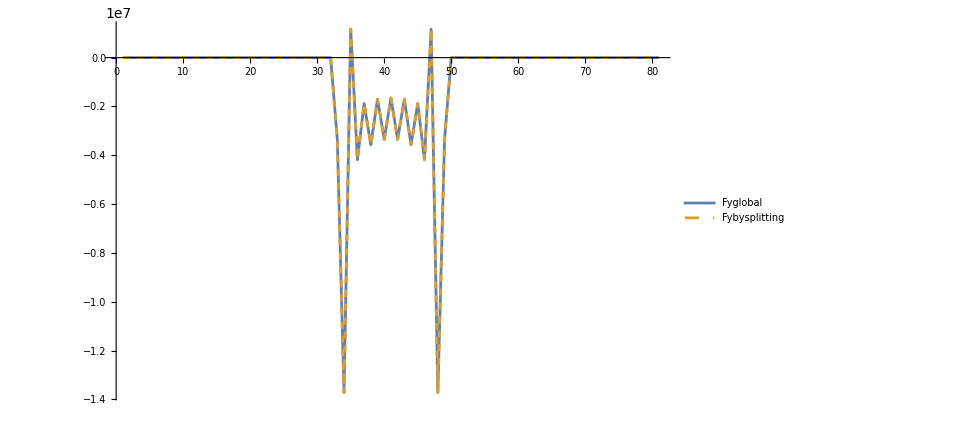

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,10).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[1;;81]];
xcoordglobal=underpunchdata[[All,2]];


Fyglobal=data[[6482;;6562]][[All,7]];
Fybysplitting={1.862645149230957*^-9,1.30385160446167*^-8,1.4901161193847656*^-8,5.587935447692871*^-9,-9.313225746154785*^-9,2.7939677238464355*^-8,-3.725290298461914*^-9,5.587935447692871*^-9,-3.725290298461914*^-9,3.725290298461914*^-9,9.313225746154785*^-9,-2.421438694000244*^-8,-3.725290298461914*^-9,-3.3527612686157227*^-8,1.862645149230957*^-9,-2.60770320892334*^-8,1.4901161193847656*^-8,-2.9802322387695312*^-8,1.4901161193847656*^-8,-4.0978193283081055*^-8,1.862645149230957*^-8,-1.4901161193847656*^-8,-2.7939677238464355*^-8,1.4901161193847656*^-8,2.7939677238464355*^-8,-2.2351741790771484*^-8,1.1175870895385742*^-8,2.2351741790771484*^-8,-5.587935447692871*^-8,-7.078051567077637*^-8,-1.7136335372924805*^-7,4.76837158203125*^-7,-3.3406874120641374*^6,-1.3720538159021407*^7,1.1677831494912207*^6,-4.1807227586771473*^6,-1.8787691262655072*^6,-3.5710460089880303*^6,-1.7014654550796226*^6,-3.348885755402416*^6,-1.653415688473288*^6,-3.3488857554023117*^6,-1.7014654550795443*^6,-3.571046008988023*^6,-1.8787691262653992*^6,-4.1807227586767375*^6,1.1677831494914442*^6,-1.3720538159018919*^7,-3.3406874120642543*^6,3.129243850708008*^-7,4.284083843231201*^-8,-2.9802322387695312*^-8,-7.450580596923828*^-9,-2.9802322387695312*^-8,-2.9802322387695312*^-8,1.1175870895385742*^-8,-1.30385160446167*^-8,-1.4901161193847656*^-8,9.313225746154785*^-10,2.2351741790771484*^-8,2.7939677238464355*^-9,5.587935447692871*^-8,1.862645149230957*^-8,-3.3527612686157227*^-8,-1.862645149230957*^-8,-4.0978193283081055*^-8,9.313225746154785*^-10,3.3527612686157227*^-8,2.1420419216156006*^-8,-3.725290298461914*^-9,-3.725290298461914*^-9,3.5390257835388184*^-8,-9.313225746154785*^-10,-1.1175870895385742*^-8,-1.862645149230957*^-9,0.,-2.3283064365386963*^-9,-1.1175870895385742*^-8,3.259629011154175*^-9,-1.6763806343078613*^-8,3.725290298461914*^-9};

ListLinePlot[{Fyglobal,Fybysplitting},PlotLegends->Placed[{"Fyglobal","Fybysplitting"},{0.7,0.3}],PlotRange->All,PlotStyle->{{},{Dashed}}]
```

```mathematica
Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=40; (*For*)
{m1,n1,m2,n2}={1,10,1,10};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[16]]={m1,n1,m2,n2, 1};
AGtype[[17]]={m1,n1,m2,n2, 2};

AGtype[[24]]={m1,n1,m2,n2, 1};
AGtype[[25]]={m1,n1,m2,n2, 2};
```

PxResultant

Nodal traction vectors P(1,1) = {-0.000,0.000,-0.000,0.000,-0.001,0.001,-0.005,0.004,-0.030,0.025,-0.173,0.148,-1.009,0.861,-5.881,5.020,-34.278,29.258,-199.787,170.529,-1164.445,993.916,-6786.881,5792.965,-39556.843,33763.877,-230554.174,196790.297,-1.344×10^6,1.147×10^6,-7.832×10^6,8.490×10^6,-2.531×10^8,-4.540×10^7,-2.071×10^7,-2.609×10^7,-2.138×10^7,-2.158×10^7,-2.025×10^7,-2.011×10^7,-1.981×10^7,-2.011×10^7,-2.025×10^7,-2.158×10^7,-2.138×10^7,-2.609×10^7,-2.071×10^7,-4.540×10^7,-2.531×10^8,8.490×10^6,-7.832×10^6,1.147×10^6,-1.344×10^6,196790.297,-230554.174,33763.877,-39556.843,5792.965,-6786.881,993.916,-1164.445,170.529,-199.787,29.258,-34.278,5.020,-5.881,0.861,-1.009,0.148,-0.173,0.025,-0.030,0.004,-0.005,0.001,-0.001,0.000,-0.000,0.000,-0.000}

p(x) resultant force P(1,1) = -6.28021×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2026_01_21_analysis element nodal force, traction\2026_01_21_punch_results\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1\NodalTraction.xlsx

-Graphics-

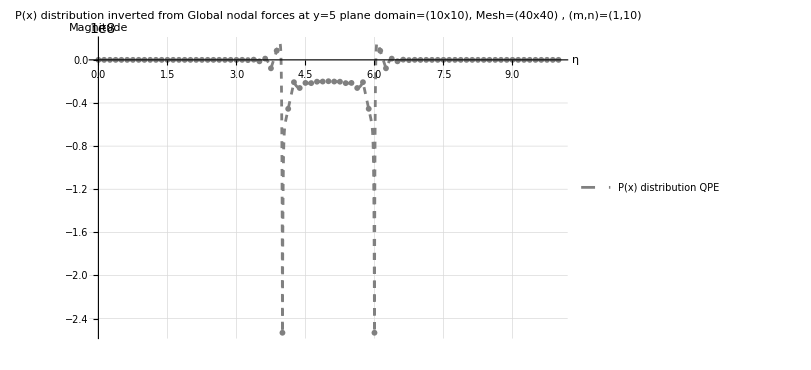

```mathematica
q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];

(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{All,All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch at y=5 plane, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]

(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.007]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE]
```

```mathematica
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
```

-Graphics-

### p(x) y=10 Frictionless punch_Geom 10x10, 40x40 mesh (m1,n1,m2,n2;ngauss)(1,10,1,10;3)_RP_TEST

#### Element force v2 (with element_id as input)

```mathematica
Clear["Global`*"]
```

```mathematica
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
estifffile="Ke_by_element.xlsx";
connfile="connectivity_Q9_40x40.xlsx";
dispfile="nodal_displacement_disp_control_(1,10).xlsx";

estiffdata=Import[FileNameJoin[{dir,estifffile}]];
conndata=Import[FileNameJoin[{dir2,connfile}]];
dispdata=Import[FileNameJoin[{dir2,dispfile}]];
(*connectivity without headers (same idea as your earlier snippet)*)
connmatrix=Drop[Drop[conndata[[1]],1],None,1];
(*nodal table without header row*)
nodaldata=Drop[dispdata[[1]],1];
(* =========================Functions=========================*)

ClearAll[estiffness,elemnodeid,nodaldispvec,elemforce];
(*Element stiffness matrix with redundant rows/cols removed*)
estiffness[elemid_Integer]:=Drop[Drop[estiffdata[[elemid+1]],{1,6}],None,{1,1}];
(*Element node IDs (Python 0-based stored in file)*)
elemnodeid[elemid_Integer]:=connmatrix[[elemid+1]];
(*Flattened displacement vector compatible with Ke*)
nodaldispvec[elemid_Integer]:=Module[{elemnode,nodalsol,nodaldisp},elemnode=elemnodeid[elemid];
nodalsol=nodaldata[[elemnode+1]];(*+1 because Mathematica is 1-based*)nodaldisp=nodalsol[[All,{4,5}]];(*columns Ux,Uy*)Flatten[nodaldisp]];
(*Element nodal force vector*)
elemforce[elemid_Integer]:=estiffness[elemid].nodaldispvec[elemid];
```

```mathematica
Ne=Length[connmatrix];  (*number of elements*)

forceMat=Table[Prepend[Flatten@elemforce[e],e],(*add elemid (0-based) as first column*){e,0,Ne-1}];

header18=Flatten@Table[{"f"<>ToString[i]<>"_1","f"<>ToString[i]<>"_2"},{i,1,9}];

header19=Prepend[header18,"elemid(py0)"];

Export[FileNameJoin[{dir2,"ElementForce.xlsx"}],Prepend[forceMat,header19],"XLSX"];
```

#### Traction along horizontal plane y=10

```mathematica
dir2="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
elenodalforce="ElementForce.xlsx";
elenodalforcedata=Import[FileNameJoin[{dir2,elenodalforce}]];

eleforcedata=Drop[Drop[elenodalforcedata[[1]],{1,0}],{1,1}];
fxY95=Take[eleforcedata[[All,{8,14,6}]],{1561,1600}];(*top edges of second row from the top*)
fyY95=Take[eleforcedata[[All,{9,15,7}]],{1561,1600}]; (*top edge of second row from the top*)

(*Length[eleforcedata]
eleforcedata[[1600]]*)

Ne=Length[fxY95];
FgxY95=ConstantArray[0,2 Ne+1];
FgyY95=ConstantArray[0,2 Ne+1];

Do[
FgxY95[[{2 e-1,2 e,2 e+1}]]+=fxY95[[e]];
FgyY95[[{2 e-1,2 e,2 e+1}]]+=fyY95[[e]];
,{e,1,40}];
FgyY95

ListLinePlot[{FgxY95,FgyY95},PlotRange->All,
PlotLegends->Placed[{
Style["fx, y=9",16],Style["fy,  y=5",16],
Style["fx, y=9.5",16],Style["fy,  y=5",16]
},{0.7,0.2}],
AxesLabel->{Style["x",16],Style["nodal force values",16]},PlotLabel->Style[Row[{" Nodal force along y=5 row elements"}],Bold,16], GridLines->Automatic,ImageSize->600]
```

{1.86265×10^-9,1.30385×10^-8,1.49012×10^-8,5.58794×10^-9,-9.31323×10^-9,2.79397×10^-8,-3.72529×10^-9,5.58794×10^-9,-3.72529×10^-9,3.72529×10^-9,9.31323×10^-9,-2.42144×10^-8,-3.72529×10^-9,-3.35276×10^-8,1.86265×10^-9,-2.6077×10^-8,1.49012×10^-8,-2.98023×10^-8,1.49012×10^-8,-4.09782×10^-8,1.86265×10^-8,-1.49012×10^-8,-2.79397×10^-8,1.49012×10^-8,2.79397×10^-8,-2.23517×10^-8,1.11759×10^-8,2.23517×10^-8,-5.58794×10^-8,-7.07805×10^-8,-1.71363×10^-7,4.76837×10^-7,-3.34069×10^6,-1.37205×10^7,1.16778×10^6,-4.18072×10^6,-1.87877×10^6,-3.57105×10^6,-1.70147×10^6,-3.34889×10^6,-1.65342×10^6,-3.34889×10^6,-1.70147×10^6,-3.57105×10^6,-1.87877×10^6,-4.18072×10^6,1.16778×10^6,-1.37205×10^7,-3.34069×10^6,3.12924×10^-7,4.28408×10^-8,-2.98023×10^-8,-7.45058×10^-9,-2.98023×10^-8,-2.98023×10^-8,1.11759×10^-8,-1.30385×10^-8,-1.49012×10^-8,9.31323×10^-10,2.23517×10^-8,2.79397×10^-9,5.58794×10^-8,1.86265×10^-8,-3.35276×10^-8,-1.86265×10^-8,-4.09782×10^-8,9.31323×10^-10,3.35276×10^-8,2.14204×10^-8,-3.72529×10^-9,-3.72529×10^-9,3.53903×10^-8,-9.31323×10^-10,-1.11759×10^-8,-1.86265×10^-9,0.,-2.32831×10^-9,-1.11759×10^-8,3.25963×10^-9,-1.67638×10^-8,3.72529×10^-9}

-Graphics-

#### p(x) y=10

PxResultant

Nodal traction vectors P(1,1) = {-0.000,0.000,-0.000,0.000,-0.000,0.000,-0.002,0.002,-0.013,0.011,-0.075,0.064,-0.435,0.371,-2.536,2.164,-14.779,12.615,-86.138,73.523,-502.049,428.525,-2926.154,2497.629,-17054.876,14557.247,-99403.102,84845.854,-579363.733,494517.879,-3.377×10^6,3.660×10^6,-1.091×10^8,-5.023×10^7,-1.625×10^7,-2.675×10^7,-2.062×10^7,-2.169×10^7,-2.011×10^7,-2.013×10^7,-1.976×10^7,-2.013×10^7,-2.011×10^7,-2.169×10^7,-2.062×10^7,-2.675×10^7,-1.625×10^7,-5.023×10^7,-1.091×10^8,3.660×10^6,-3.377×10^6,494517.879,-579363.733,84845.854,-99403.102,14557.247,-17054.876,2497.629,-2926.154,428.525,-502.049,73.523,-86.138,12.615,-14.779,2.164,-2.536,0.371,-0.435,0.064,-0.075,0.011,-0.013,0.002,-0.002,0.000,-0.000,0.000,-0.000,0.000,-0.000}

p(x) resultant force P(1,1) = -5.95779×10^7

C:\Users\nguye\OneDrive - UCB-O365\Haden\Los Alamos NL\Work\2026_01_21_analysis element nodal force, traction\2026_01_21_punch_results\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1\NodalTraction.xlsx

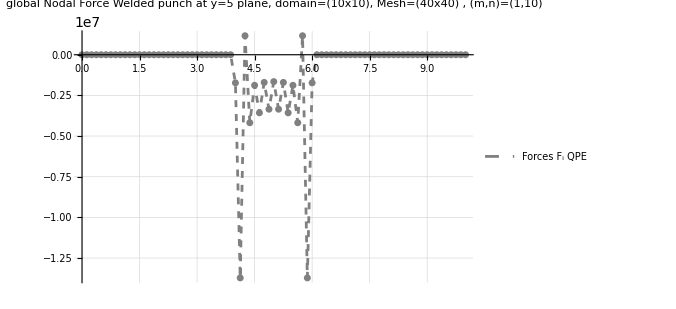

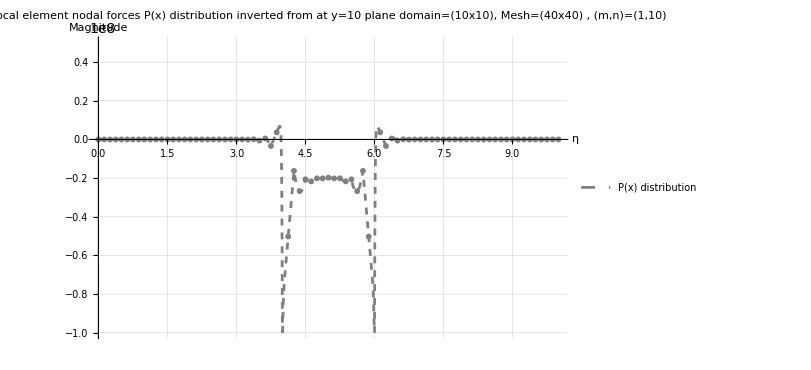

```mathematica
(*Get the nodal force from Python*)
dir="C:\\Users\\nguye\\OneDrive - UCB-O365\\Haden\\Los Alamos NL\\Work\\2026_01_21_analysis element nodal force, traction\\2026_01_21_punch_results\\disp_control(40,40)_rigid_punch_(1,10,1,10,10)_dz=-0.1";
filename="nodal_displacement_disp_control_(1,10).xlsx";
{data}=Import[FileNameJoin[{dir,filename}]];
raw=Rest[data];
underpunchdata=raw[[1;;81]];
xcoordglobal=underpunchdata[[All,2]];
Fy={1.862645149230957*^-9,1.30385160446167*^-8,1.4901161193847656*^-8,5.587935447692871*^-9,-9.313225746154785*^-9,2.7939677238464355*^-8,-3.725290298461914*^-9,5.587935447692871*^-9,-3.725290298461914*^-9,3.725290298461914*^-9,9.313225746154785*^-9,-2.421438694000244*^-8,-3.725290298461914*^-9,-3.3527612686157227*^-8,1.862645149230957*^-9,-2.60770320892334*^-8,1.4901161193847656*^-8,-2.9802322387695312*^-8,1.4901161193847656*^-8,-4.0978193283081055*^-8,1.862645149230957*^-8,-1.4901161193847656*^-8,-2.7939677238464355*^-8,1.4901161193847656*^-8,2.7939677238464355*^-8,-2.2351741790771484*^-8,1.1175870895385742*^-8,2.2351741790771484*^-8,-5.587935447692871*^-8,-7.078051567077637*^-8,-1.7136335372924805*^-7,4.76837158203125*^-7,-1728595.43773108,-1.3720538159021407*^7,1.1677831494912207*^6,-4.1807227586771473*^6,-1.8787691262655072*^6,-3.5710460089880303*^6,-1.7014654550796226*^6,-3.348885755402416*^6,-1.653415688473288*^6,-3.3488857554023117*^6,-1.7014654550795443*^6,-3.571046008988023*^6,-1.8787691262653992*^6,-4.1807227586767375*^6,1.1677831494914442*^6,-1.3720538159018919*^7,-1728595.43773108,3.129243850708008*^-7,4.284083843231201*^-8,-2.9802322387695312*^-8,-7.450580596923828*^-9,-2.9802322387695312*^-8,-2.9802322387695312*^-8,1.1175870895385742*^-8,-1.30385160446167*^-8,-1.4901161193847656*^-8,9.313225746154785*^-10,2.2351741790771484*^-8,2.7939677238464355*^-9,5.587935447692871*^-8,1.862645149230957*^-8,-3.3527612686157227*^-8,-1.862645149230957*^-8,-4.0978193283081055*^-8,9.313225746154785*^-10,3.3527612686157227*^-8,2.1420419216156006*^-8,-3.725290298461914*^-9,-3.725290298461914*^-9,3.5390257835388184*^-8,-9.313225746154785*^-10,-1.1175870895385742*^-8,-1.862645149230957*^-9,0.,-2.3283064365386963*^-9,-1.1175870895385742*^-8,3.259629011154175*^-9,-1.6763806343078613*^-8,3.725290298461914*^-9};


Clear[x]
nx=40;
ny=40;
gx=10; gy=10;
nele=40; (*For*)
{m1,n1,m2,n2}={1,10,1,10};
AGtype=Table[{1,1,1,1,1},{i,1,nele}];
AGtype[[16]]={m1,n1,m2,n2, 1};
AGtype[[17]]={m1,n1,m2,n2, 2};

AGtype[[24]]={m1,n1,m2,n2, 1};
AGtype[[25]]={m1,n1,m2,n2, 2};

q2LineConnectivity[ne_Integer]:=Partition[Range[2 ne+1],3,2]
conns=q2LineConnectivity[nele];

(****************)
(*Input*)
xcoord=Partition[xcoordglobal,3,2];(*element nodal x-coordinate*)

Mmat=GlobalMmat[xcoord,conns,AGtype]; (*Global M matrix*)
Pvec=LinearSolve[Mmat,Fy]; (* Compute Nodal traction vector *)

Pxdata=PxinterpolatedData[Pvec,AGtype,xcoord];
Pvecdata=Transpose[{xcoordglobal,Pvec}];
totalResutant=ComputeResultant[Pelem,xcoord,AGtype];
Print[Style[Row[{"Nodal traction vectors P(",m,",",n,") = ", NumberForm[Pvec,{Infinity,3}]}],16, Bold,Blue]];
Print[Style[Row[{"p(x) resultant force P(",m,",",n,") = ", totalResutant}],16,Bold,Red]];
Export[FileNameJoin[{dir,"NodalTraction.xlsx"}],Pvec]

Fydata=Transpose[{xcoordglobal,Fy}];

FvecPlotQPE=ListLinePlot[Fydata,PlotStyle->{Gray,Dashed},PlotRange->{All,All},PlotLegends->Placed[{"Forces F_i QPE"},{0.7,0.3}],PlotLabel->Style[Row[{"global Nodal Force Welded punch at y=5 plane, \n domain=(",gx,"x",gy,"), Mesh=(", 40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],Bold,16], GridLines->Automatic,ImageSize->500,TicksStyle->Directive["Label",Bold, 12]];
FvecDotQPE=ListPlot[Fydata,PlotStyle->{Gray,PointSize[0.01]}];

Show[FvecPlotQPE,FvecDotQPE]

(**********************)
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,{-1*10^8,5*10^7}},PlotStyle->{Gray,Dashed},PlotLegends->Placed[{"P(x) distribution"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" Local element nodal forces P(x) distribution inverted from at y=10 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

PvecPlotQPE=ListPlot[Pvecdata,PlotStyle->{Gray,PointSize[0.007]}(*PlotLegends->Placed[{"Nodal traction P_i"},{0.8,0.3}]*)];

Show[PxplotQPE,PvecPlotQPE]
```

```mathematica
PxplotQPE=ListLinePlot[Pxdata,PlotRange->{All,All},PlotStyle->{Gray},PlotLegends->Placed[{"P(x) distribution QPE"},{0.7,0.3}],AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces at y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
```

-Graphics-

### Gauss Point stress

#### Gauss point stresses

```mathematica
yBelow=9.47182;
yAbove=9.52818;
xyBelow={{0.02817541634481457,241645.9936879174},{0.125,241835.5402205195},{0.2218245836551855,221135.4479114301},{0.2781754163448146,206893.8539859416},{0.375,177038.2937291194},{0.4718245836551855,144557.5161097222},{0.5281754163448147,126039.0795938101},{0.625,94565.24154154786},{0.7218245836551855,67032.03997803546},{0.7781754163448147,52001.59499021771},{0.875,26870.11151983732},{0.9718245836551856,6825.592001522338},{1.028175416344815,-4201.976167266432},{1.125,-23613.91498229686},{1.221824583655186,-37896.86431633934},{1.278175416344815,-46227.10692999141},{1.375,-62514.74722619989},{1.471824583655186,-73538.47598461299},{1.528175416344815,-80727.65920202255},{1.625,-96823.11567179463},{1.721824583655186,-107252.0218313511},{1.778175416344814,-114978.0599432207},{1.875,-134303.7310770296},{1.971824583655186,-147441.9835742418},{2.028175416344815,-157930.8559596967},{2.125,-185449.2482617745},{2.221824583655186,-206653.0502013023},{2.278175416344815,-223724.1610888363},{2.375,-268330.7666323063},{2.471824583655186,-308474.9532419227},{2.528175416344815,-340090.5075749264},{2.625,-420418.9185953273},{2.721824583655186,-505333.0462860663},{2.778175416344815,-570493.315303111},{2.875,-730565.6104694158},{2.971824583655186,-929703.6674486265},{3.028175416344815,-1.078673174095058*^6},{3.125,-1.433710156010348*^6},{3.221824583655186,-1.953607509212316*^6},{3.278175416344815,-2.329646831206722*^6},{3.375,-3.200460901808295*^6},{3.471824583655186,-4.653596526720367*^6},{3.528175416344815,-5.668641173307073*^6},{3.625,-7.850001192931185*^6},{3.721824583655186,-1.121777187735447*^7},{3.778175416344815,-1.327983024494028*^7},{3.875,-1.722100819283722*^7},{3.971824583655186,-2.092894562668249*^7},{4.028175416344816,-2.275348330226822*^7},{4.125,-2.516036923998373*^7},{4.221824583655186,-2.562086470726626*^7},{4.278175416344815,-2.567893720759983*^7},{4.375,-2.506362304219391*^7},{4.471824583655186,-2.422745159220006*^7},{4.528175416344816,-2.373661436135402*^7},{4.625,-2.281329083996928*^7},{4.721824583655186,-2.222203575121454*^7},{4.778175416344816,-2.19265619863211*^7},{4.875,-2.15236939472853*^7},{4.971824583655186,-2.14180981875558*^7},{5.028175416344816,-2.141809818755598*^7},{5.125,-2.152369394728539*^7},{5.221824583655186,-2.192656198631977*^7},{5.278175416344816,-2.222203575121304*^7},{5.375,-2.281329083996841*^7},{5.471824583655186,-2.37366143613524*^7},{5.528175416344816,-2.422745159219814*^7},{5.625,-2.506362304219218*^7},{5.721824583655186,-2.567893720759827*^7},{5.778175416344816,-2.562086470726456*^7},{5.875,-2.516036923998173*^7},{5.971824583655186,-2.27534833022689*^7},{6.028175416344815,-2.092894562668325*^7},{6.125,-1.722100819283646*^7},{6.221824583655186,-1.327983024493924*^7},{6.278175416344816,-1.121777187735347*^7},{6.375,-7.850001192930773*^6},{6.471824583655187,-5.668641173306382*^6},{6.528175416344816,-4.653596526719684*^6},{6.625,-3.200460901808188*^6},{6.721824583655186,-2.329646831206434*^6},{6.778175416344816,-1.953607509212334*^6},{6.875,-1.433710156011034*^6},{6.971824583655185,-1.078673174095142*^6},{7.028175416344815,-929703.6674487167},{7.125,-730565.6104703536},{7.221824583655186,-570493.3153038423},{7.278175416344815,-505333.0462867285},{7.375,-420418.918596089},{7.471824583655185,-340090.5075753184},{7.528175416344816,-308474.9532420893},{7.625,-268330.7666323783},{7.721824583655185,-223724.1610888412},{7.778175416344816,-206653.0502011724},{7.875,-185449.2482614913},{7.971824583655186,-157930.8559598188},{8.028175416344816,-147441.9835744791},{8.125,-134303.7310767805},{8.221824583655186,-114978.0599427899},{8.278175416344816,-107252.0218311673},{8.375,-96823.1156718705},{8.471824583655188,-80727.65920242138},{8.528175416344816,-73538.47598466181},{8.625,-62514.74722571264},{8.721824583655186,-46227.10692948016},{8.778175416344816,-37896.86431587054},{8.875,-23613.91498207521},{8.971824583655188,-4201.976166651526},{9.028175416344816,6825.592001852012},{9.125,26870.11151984645},{9.221824583655186,52001.59499012023},{9.278175416344816,67032.03997820336},{9.375,94565.2415417073},{9.471824583655186,126039.0795940605},{9.528175416344816,144557.5161100142},{9.625,177038.2937294914},{9.721824583655186,206893.8539861396},{9.778175416344816,221135.4479115155},{9.875,241835.5402202414},{9.971824583655188,241645.9936877347}};

xyAbove={{0.02817541634481458,178652.6588008479},{0.125,197408.2426034907},{0.2218245836551854,184026.9819204107},{0.2781754163448146,172703.6997248716},{0.375,149416.5541120507},{0.4718245836551855,121807.3886612145},{0.5281754163448147,106029.4666446358},{0.625,79784.34225879522},{0.7218245836551854,56696.98400183584},{0.7781754163448148,44228.17838895584},{0.875,23644.13022602339},{0.9718245836551856,7394.296538478899},{1.028175416344815,-1494.894655892247},{1.125,-17136.03892894465},{1.221824583655186,-28203.96832036847},{1.278175416344815,-34722.20315110596},{1.375,-47708.33666910074},{1.471824583655186,-55720.09317838331},{1.528175416344815,-61161.87803860725},{1.625,-73897.78162567315},{1.721824583655186,-80939.0507336496},{1.778175416344814,-86604.3779412338},{1.875,-101779.52473726},{1.971824583655185,-110263.8197079312},{2.028175416344815,-117791.0844556675},{2.125,-139214.0650533635},{2.221824583655186,-152902.7550084429},{2.278175416344815,-165038.9719352728},{2.375,-199469.1296734304},{2.471824583655186,-225940.2864453911},{2.528175416344815,-248451.2458081398},{2.625,-310074.799232345},{2.721824583655186,-367466.4021922328},{2.778175416344815,-414747.661815525},{2.875,-537865.6452035252},{2.971824583655186,-675526.2666129353},{3.028175416344815,-790188.3578483644},{3.125,-1.071565828788189*^6},{3.221824583655186,-1.440427607809528*^6},{3.278175416344815,-1.771642714346036*^6},{3.375,-2.535806061544937*^6},{3.471824583655186,-3.65055657415615*^6},{3.528175416344815,-4.733618549983783*^6},{3.625,-7.143408232950474*^6},{3.721824583655186,-1.079013872126528*^7},{3.778175416344815,-1.320388396544716*^7},{3.875,-1.754897820057895*^7},{3.971824583655185,-2.18685760314464*^7},{4.028175416344815,-2.389233226322502*^7},{4.125,-2.65949884672168*^7},{4.221824583655186,-2.689519591096752*^7},{4.278175416344816,-2.672904021931541*^7},{4.375,-2.58790494841336*^7},{4.471824583655186,-2.45754212396651*^7},{4.528175416344816,-2.381296087994201*^7},{4.625,-2.278408121485113*^7},{4.721824583655186,-2.208701095459956*^7},{4.778175416344815,-2.174221544366556*^7},{4.875,-2.132234947872482*^7},{4.971824583655185,-2.119860109459522*^7},{5.028175416344816,-2.119860109459481*^7},{5.125,-2.132234947872465*^7},{5.221824583655186,-2.174221544366666*^7},{5.278175416344816,-2.208701095460076*^7},{5.375,-2.278408121485034*^7},{5.471824583655186,-2.381296087994173*^7},{5.528175416344814,-2.457542123966428*^7},{5.625,-2.587904948413146*^7},{5.721824583655186,-2.672904021931271*^7},{5.778175416344814,-2.689519591096519*^7},{5.875,-2.659498846721418*^7},{5.971824583655185,-2.389233226322297*^7},{6.028175416344815,-2.186857603144442*^7},{6.125,-1.754897820057757*^7},{6.221824583655186,-1.320388396544692*^7},{6.278175416344816,-1.079013872126506*^7},{6.375,-7.143408232950537*^6},{6.471824583655185,-4.733618549983874*^6},{6.528175416344815,-3.650556574156051*^6},{6.625,-2.535806061544783*^6},{6.721824583655185,-1.771642714346513*^6},{6.778175416344816,-1.440427607809777*^6},{6.875,-1.071565828788017*^6},{6.971824583655185,-790188.3578486745},{7.028175416344815,-675526.266613612},{7.125,-537865.6452047136},{7.221824583655186,-414747.6618166753},{7.278175416344816,-367466.4021931445},{7.375,-310074.7992326689},{7.471824583655185,-248451.2458085108},{7.528175416344815,-225940.2864457754},{7.625,-199469.1296736523},{7.721824583655187,-165038.9719357295},{7.778175416344816,-152902.7550088436},{7.875,-139214.0650536633},{7.971824583655186,-117791.0844557653},{8.028175416344816,-110263.8197077053},{8.125,-101779.5247373916},{8.221824583655184,-86604.3779413222},{8.278175416344816,-80939.05073367128},{8.375,-73897.78162559046},{8.471824583655188,-61161.87803873268},{8.528175416344816,-55720.09317850671},{8.625,-47708.33666947365},{8.721824583655186,-34722.20315145823},{8.778175416344816,-28203.96832034513},{8.875,-17136.03892869994},{8.971824583655186,-1494.894656225835},{9.028175416344816,7394.296538163995},{9.125,23644.13022593712},{9.221824583655186,44228.17838882139},{9.278175416344816,56696.98400148723},{9.375,79784.34225867038},{9.471824583655188,106029.4666444516},{9.528175416344816,121807.3886609783},{9.625,149416.5541118728},{9.721824583655184,172703.6997245677},{9.778175416344816,184026.9819202248},{9.875,197408.2426035478},{9.971824583655188,178652.6588006642}};
```

#### Gauss point stresses plot

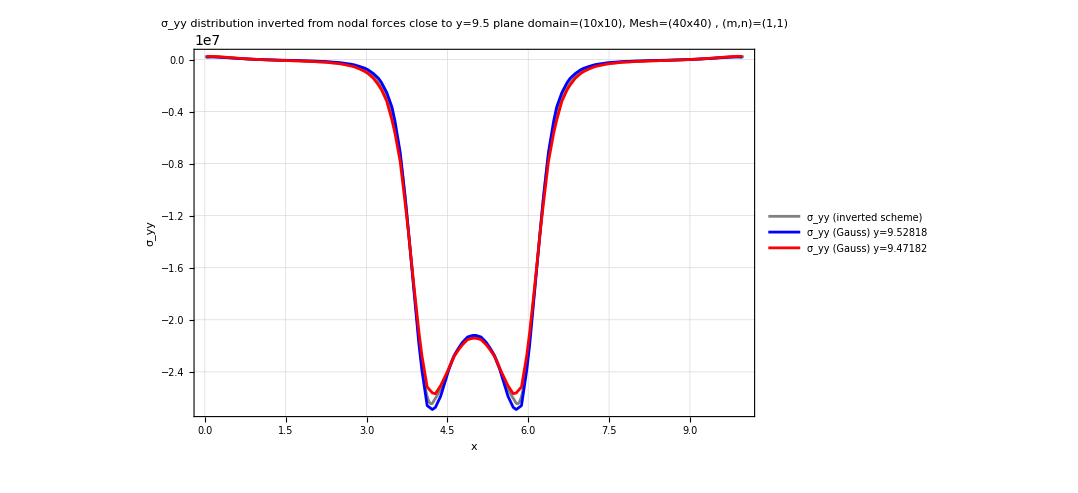

```mathematica
ListLinePlot[{xyAbove,xyBelow},PlotRange->{All,All},
PlotStyle->{Blue, Red},
PlotLegends->Placed[{
"sigma_yy (Gauss) y="<>ToString[yAbove],
"sigma_yy (Gauss) y="<>ToString[yBelow]},{0.7,0.3}],
AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces close to y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600];

ListLinePlot[{Pxdata,xyAbove,xyBelow},PlotRange->{All,All},
PlotStyle->{Gray,Blue, Red},
PlotLegends->Placed[{
"σ_yy (inverted scheme)",
"σ_yy (Gauss) y="<>ToString[yAbove],
"σ_yy (Gauss) y="<>ToString[yBelow]},{0.8,0.35}],
Frame->True,FrameLabel->{Style["x",Bold,16],Style["σ_yy",Bold,16]},PlotLabel->Style[Row[{" σ_yy distribution inverted from nodal forces close to y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->500]
```

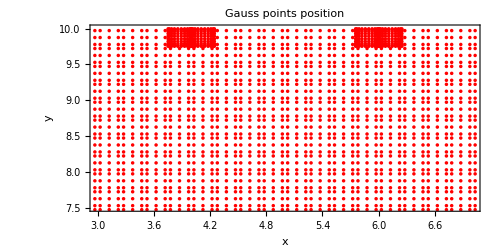

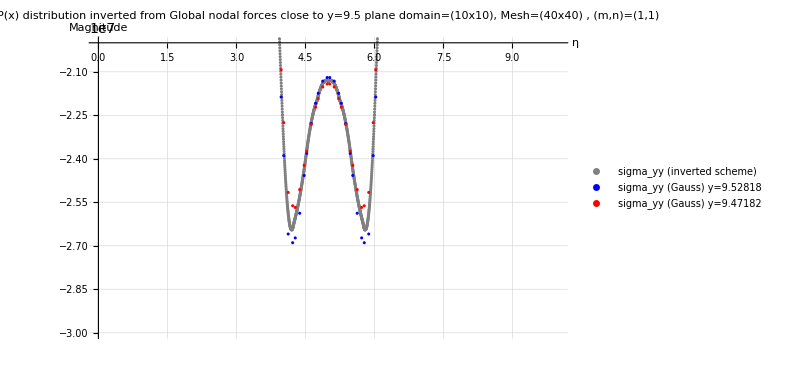

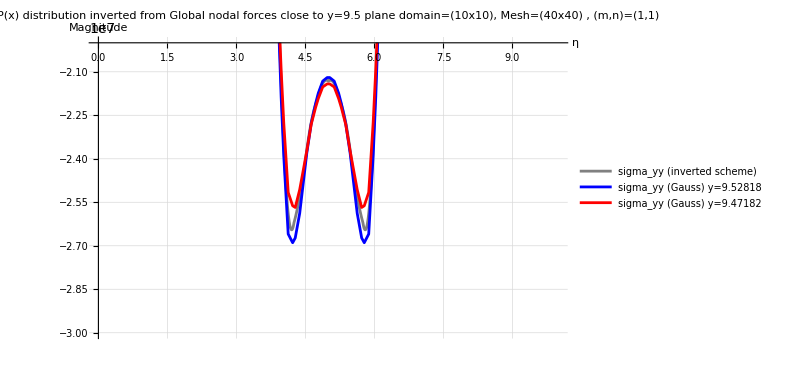

```mathematica
ListPlot[{Pxdata,xyAbove,xyBelow},PlotRange->{All,{-2*10^7,-3*10^7}},
PlotStyle->{Gray,Blue, Red},
PlotLegends->Placed[{
"sigma_yy (inverted scheme)",
"sigma_yy (Gauss) y="<>ToString[yAbove],
"sigma_yy (Gauss) y="<>ToString[yBelow]},{0.8,0.3}],
AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces close to y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
ListLinePlot[{Pxdata,xyAbove,xyBelow},PlotRange->{All,{-2*10^7,-3*10^7}},
PlotStyle->{Gray,Blue, Red},
PlotLegends->Placed[{
"sigma_yy (inverted scheme)",
"sigma_yy (Gauss) y="<>ToString[yAbove],
"sigma_yy (Gauss) y="<>ToString[yBelow]},{0.8,0.3}],
AxesLabel->{Style["η",16],Style["Magnitude",16]},PlotLabel->Style[Row[{" P(x) distribution inverted from Global nodal forces close to y=9.5 plane \n domain=(",gx,"x",gy,"), Mesh=(",40,"x",ny,") , (m,n)=(",m1,",",n1,")"}],16], GridLines->Automatic,ImageSize->600]
```